## G=6 models

### Setup

```mathematica
SetDirectory@ParentDirectory@NotebookDirectory[];
<<QuiverGaugeTheory`
<<InterfaceM2`
```

```mathematica
<<MaTeX`
```

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"functions.wl"}]
$ImportData=True;
$DataDirectory=FileNameJoin[{NotebookDirectory[],"data"}];
$FiguresDirectory=FileNameJoin[{NotebookDirectory[],"figures"}];
```

### Model 7: PdP_(3a) = ℂ^3/ℤ_6 (1,2,3)

```mathematica
WPdP3a=-(Subscript[X, 1][1,2]·Subscript[X, 1][2,5]·Subscript[X, 1][5,1])+Subscript[X, 1][1,2]·Subscript[X, 1][2,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,1]+Subscript[X, 1][1,3]·Subscript[X, 1][3,5]·Subscript[X, 1][5,1]+Subscript[X, 1][1,5]·Subscript[X, 1][5,4]·Subscript[X, 1][4,1]-Subscript[X, 1][1,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,4]·Subscript[X, 1][4,3]·Subscript[X, 1][3,2]-Subscript[X, 1][2,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,2]+Subscript[X, 1][2,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,3]·Subscript[X, 1][3,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,3]-Subscript[X, 1][3,5]·Subscript[X, 1][5,4]·Subscript[X, 1][4,3];
```

```mathematica
PdP3a=Model["PdP3a","Descriptions"->{"ℂ","PdP"},"Potential"->WPdP3a,"QuiverPositioning"->{6,3,4,5,2,1}];
```

### Model 8: PdP_(3c)

```mathematica
WPdP3cPhaseA=-(Subscript[X, 1][1,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,1])+Subscript[X, 1][2,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]+Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]-Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,1]-Subscript[X, 1][1,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2];
```

```mathematica
WPdP3cPhaseB=Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,2]·Subscript[X, 1][2,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,5]·Subscript[X, 2][5,3]·Subscript[X, 1][3,1]-Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,2]+Subscript[X, 1][2,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]+Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]+Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 2][5,3]-Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]+Subscript[X, 1][1,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,1]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2];
```

```mathematica
PdP3cPhaseA=Model[{"PdP3c","PhaseA"},"Potential"->WPdP3cPhaseA,"QuiverPositioning"->{5,3,4,6,2,1}];
PdP3cPhaseB=Model[{"PdP3c","PhaseB"},"Potential"->WPdP3cPhaseB,"QuiverPositioning"->{2,{1,4},6,3,5}];
```

### Model 9: PdP_(3b)

```mathematica
WPdP3bPhaseA=-(Subscript[X, 1][1,2]·Subscript[X, 1][2,5]·Subscript[X, 1][5,1])+Subscript[X, 1][1,2]·Subscript[X, 1][2,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1]+Subscript[X, 1][1,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,2]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,1]-Subscript[X, 1][2,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2];
```

```mathematica
WPdP3bPhaseB=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1])+Subscript[X, 1][2,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,2]+Subscript[X, 1][3,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,3]-Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]+Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,1]-Subscript[X, 1][1,6]·Subscript[X, 1][6,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,1]+Subscript[X, 1][1,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2];
```

```mathematica
WPdP3bPhaseC=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1])+Subscript[X, 1][1,3]·Subscript[X, 1][3,5]·Subscript[X, 1][5,1]+Subscript[X, 1][1,6]·Subscript[X, 2][6,2]·Subscript[X, 1][2,1]+Subscript[X, 1][2,4]·Subscript[X, 1][4,3]·Subscript[X, 2][3,2]-Subscript[X, 1][2,4]·Subscript[X, 1][4,6]·Subscript[X, 2][6,2]-Subscript[X, 1][2,5]·Subscript[X, 1][5,3]·Subscript[X, 2][3,2]+Subscript[X, 1][3,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,3]-Subscript[X, 1][3,5]·Subscript[X, 1][5,4]·Subscript[X, 1][4,3]-Subscript[X, 1][1,6]·Subscript[X, 1][6,2]·Subscript[X, 2][2,5]·Subscript[X, 1][5,1]+Subscript[X, 1][2,5]·Subscript[X, 1][5,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,2];
```

```mathematica
PdP3bPhaseA=Model[{"PdP3b","PhaseA"},"Potential"->WPdP3bPhaseA,"QuiverPositioning"->{1,4,3,2,5,6}];
PdP3bPhaseB=Model[{"PdP3b","PhaseB"},"Potential"->WPdP3bPhaseB,"QuiverPositioning"->{1,4,3,2,5,6}];
PdP3bPhaseC=Model[{"PdP3b","PhaseC"},"Potential"->WPdP3bPhaseC,"QuiverPositioning"->{6,{4,1},5,3,2}];
```

### Model 10: dP_3

```mathematica
WdP3PhaseA=Subscript[X, 1][1,3]·Subscript[X, 1][3,2]·Subscript[X, 1][2,1]+Subscript[X, 1][4,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,4]-Subscript[X, 1][1,3]·Subscript[X, 1][3,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2]·Subscript[X, 1][2,1]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,3]·Subscript[X, 1][3,2]+Subscript[X, 1][1,4]·Subscript[X, 1][4,3]·Subscript[X, 1][3,5]·Subscript[X, 1][5,2]·Subscript[X, 1][2,6]·Subscript[X, 1][6,1];
```

```mathematica
WdP3PhaseB=Subscript[X, 1][1,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1]-Subscript[X, 1][1,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]+Subscript[X, 1][5,6]·Subscript[X, 1][6,4]·Subscript[X, 2][4,5]+Subscript[X, 1][1,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2]·Subscript[X, 1][2,6]·Subscript[X, 1][6,1]-Subscript[X, 1][1,4]·Subscript[X, 2][4,5]·Subscript[X, 1][5,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,1];
```

```mathematica
WdP3PhaseC=Subscript[X, 1][1,3]·Subscript[X, 2][3,4]·Subscript[X, 1][4,1]-Subscript[X, 1][1,6]·Subscript[X, 2][6,4]·Subscript[X, 1][4,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]-Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,1]+Subscript[X, 1][1,6]·Subscript[X, 1][6,4]·Subscript[X, 2][4,5]·Subscript[X, 1][5,1]-Subscript[X, 1][2,3]·Subscript[X, 2][3,4]·Subscript[X, 2][4,5]·Subscript[X, 1][5,2]+Subscript[X, 1][2,6]·Subscript[X, 2][6,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,2];
```

```mathematica
WdP3PhaseD=-(Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 2][4,1])+Subscript[X, 1][1,3]·Subscript[X, 2][3,4]·Subscript[X, 1][4,1]+Subscript[X, 1][1,5]·Subscript[X, 1][5,4]·Subscript[X, 2][4,1]-Subscript[X, 1][1,5]·Subscript[X, 2][5,4]·Subscript[X, 3][4,1]+Subscript[X, 1][1,6]·Subscript[X, 1][6,4]·Subscript[X, 3][4,1]-Subscript[X, 1][1,6]·Subscript[X, 2][6,4]·Subscript[X, 1][4,1]+Subscript[X, 1][2,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]-Subscript[X, 1][2,3]·Subscript[X, 2][3,4]·Subscript[X, 2][4,2]-Subscript[X, 1][2,5]·Subscript[X, 1][5,4]·Subscript[X, 3][4,2]+Subscript[X, 1][2,5]·Subscript[X, 2][5,4]·Subscript[X, 2][4,2]-Subscript[X, 1][2,6]·Subscript[X, 1][6,4]·Subscript[X, 1][4,2]+Subscript[X, 1][2,6]·Subscript[X, 2][6,4]·Subscript[X, 3][4,2];
```

```mathematica
dP3PhaseA=Model[{"dP3","PhaseA"},"Potential"->WdP3PhaseA,"QuiverPositioning"->{3,4,1,6,2,5}];
dP3PhaseB=Model[{"dP3","PhaseB"},"Potential"->WdP3PhaseB,"QuiverPositioning"->{2,{6,3},1,4,5}];
dP3PhaseC=Model[{"dP3","PhaseC"},"Potential"->WdP3PhaseC,"QuiverPositioning"->{5,{1,2},{3,6},4}];
dP3PhaseD=Model[{"dP3","PhaseD"},"Potential"->WdP3PhaseD,"QuiverPositioning"->{{3,5,6},4,{1,2}}];
```

## Deformations

### PdP_(3a) ⟹ PdP_(3c) (a)

#### Deformation 1: (1→5→1) – (2→6→2)

```mathematica
PdP3aDef1η=Subscript[X, 1][1,2]·Subscript[X, 1][2,5]·Subscript[X, 1][5,6]·Subscript[X, 1][6,1];
WPdP3aDef1=WPdP3a+μ(Subscript[X, 1][1,5]·Subscript[X, 1][5,1]-Subscript[X, 1][2,6]·Subscript[X, 1][6,2]);
WPdP3aDef1Min=WPdP3aDef1//IntegrateOutMassTerms//Simplify//Expand
```

-(X_1[1,3]·X_1[3,4]·X_1[4,1])+X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,5]·X_1[5,4]·X_1[4,3]-(X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1])/μ+(X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1])/μ-(X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1])/μ+(X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1])/μ+(X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2])/μ-(X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2])/μ

```mathematica
RedefChoice1={Subscript[γ, 1][4,3]->Subscript[γ, 1][3,4],Subscript[γ, 1][3,4]->(-1/μ-Subscript[β, 1][3,4]),Subscript[α, 1][3,4]->1/μ,Subscript[β, 1][4,3]->Subscript[β, 1][3,4],Subscript[α, 1][4,3]->1/μ};
RedefRules1=FieldRedefinition[{Subscript[X, 1][3,4],Subscript[X, 1][4,3]},QuiverFromFields[WPdP3a],2]//.RedefChoice1;
RedefRules1Mass= {Subscript[X, 1][4,1]->μ Subscript[X, 1][4,1],Subscript[X, 1][4,3]->μ Subscript[X, 1][4,3],Subscript[X, 1][6,1]->μ Subscript[X, 1][6,1],Subscript[X, 1][6,3]->μ Subscript[X, 1][6,3]};
RedefRules1//Column
RedefRules1Mass//Column
```

X_1[3,4]→X_1[3,2]·X_1[2,4] (-1/μ-β_1[3,4])+X_1[3,5]·X_1[5,4] β_1[3,4]+X_1[3,4]/μ
X_1[4,3]→X_1[4,1]·X_1[1,3] (-1/μ-β_1[3,4])+X_1[4,6]·X_1[6,3] β_1[3,4]+X_1[4,3]/μ

X_1[4,1]→μ X_1[4,1]
X_1[4,3]→μ X_1[4,3]
X_1[6,1]→μ X_1[6,1]
X_1[6,3]→μ X_1[6,3]

```mathematica
DG[FieldCases[RedefRules1]/.RedefRules1,{FieldCases[RedefRules1]}]/.{Untrace->1}//Det
```

1/μ^2

```mathematica
(WPdP3aDef1Min/.RedefRules1/.RedefRules1Mass)//FTermsTable
```

X_1[1,2] | X_1[2,4]·X_1[4,6]·X_1[6,1] -1+X_1[2,5]·X_1[5,4]·X_1[4,1] 1 | 0 | 2
X_1[1,3] | X_1[3,4]·X_1[4,1] -1+X_1[3,5]·X_1[5,6]·X_1[6,1] 1 | 0 | 2
X_1[2,4] | X_1[4,6]·X_1[6,1]·X_1[1,2] -1+X_1[4,3]·X_1[3,2] 1 | 0 | 2
X_1[2,5] | X_1[5,6]·X_1[6,3]·X_1[3,2] -1+X_1[5,4]·X_1[4,1]·X_1[1,2] 1 | 0 | 2
X_1[3,2] | X_1[2,5]·X_1[5,6]·X_1[6,3] -1+X_1[2,4]·X_1[4,3] 1 | 0 | 2
X_1[3,4] | X_1[4,1]·X_1[1,3] -1+X_1[4,6]·X_1[6,3] 1 | 0 | 2
X_1[3,5] | X_1[5,4]·X_1[4,3] -1+X_1[5,6]·X_1[6,1]·X_1[1,3] 1 | 0 | 2
X_1[4,1] | X_1[1,3]·X_1[3,4] -1+X_1[1,2]·X_1[2,5]·X_1[5,4] 1 | 0 | 2
X_1[4,3] | X_1[3,5]·X_1[5,4] -1+X_1[3,2]·X_1[2,4] 1 | 0 | 2
X_1[4,6] | X_1[6,1]·X_1[1,2]·X_1[2,4] -1+X_1[6,3]·X_1[3,4] 1 | 0 | 2
X_1[5,4] | X_1[4,3]·X_1[3,5] -1+X_1[4,1]·X_1[1,2]·X_1[2,5] 1 | 0 | 2
X_1[5,6] | X_1[6,3]·X_1[3,2]·X_1[2,5] -1+X_1[6,1]·X_1[1,3]·X_1[3,5] 1 | 0 | 2
X_1[6,1] | X_1[1,2]·X_1[2,4]·X_1[4,6] -1+X_1[1,3]·X_1[3,5]·X_1[5,6] 1 | 0 | 2
X_1[6,3] | X_1[3,2]·X_1[2,5]·X_1[5,6] -1+X_1[3,4]·X_1[4,6] 1 | 0 | 2

```mathematica
WPdP3cAFromDef1=Simplify[WPdP3aDef1Min/.RedefRules1/.RedefRules1Mass]
```

-(X_1[1,3]·X_1[3,4]·X_1[4,1])+X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,5]·X_1[5,4]·X_1[4,3]-X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]+X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]+X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]-X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2]

```mathematica
Simplify[μ WPdP3aDef1Min/.{Subscript[X, 1][2,5]->μ Subscript[X, 1][2,5],Subscript[X, 1][4,1]->(Subscript[X, 1][4,1])/μ,Subscript[X, 1][4,3]->(Subscript[X, 1][4,3])/μ,Subscript[X, 1][6,3]->(Subscript[X, 1][6,3])/μ}]
(WPdP3cAFromDef1+ν Total@ZigZagOperator[WPdP3cAFromDef1][PdP3aDef1η])//IntegrateOutMassTerms
Collect[%-%%,_CenterDot,Highlighted]
```

-(X_1[1,3]·X_1[3,4]·X_1[4,1])+X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,5]·X_1[5,4]·X_1[4,3]-X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]+X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]-(X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1])/μ+X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]+(X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2])/μ-X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2]

-(X_1[1,3]·X_1[3,4]·X_1[4,1])+X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,5]·X_1[5,4]·X_1[4,3]-X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]+X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]-ν X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1]+X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]+ν X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2]-X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2]

X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1] 1/μ-ν+X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2] -1/μ+ν

```mathematica
(WPdP3cAFromDef1+ν Total@ZigZagOperator[WPdP3cAFromDef1][PdP3aDef1η])/.{Subscript[X, 1][3,4]->Subscript[X, 1][3,2]·Subscript[X, 1][2,4] (-ν-Subscript[β, 1][4,3])+Subscript[X, 1][3,5]·Subscript[X, 1][5,4] Subscript[β, 1][4,3]+Subscript[X, 1][3,4],Subscript[X, 1][4,3]->Subscript[X, 1][4,1]·Subscript[X, 1][1,3] (-ν-Subscript[β, 1][4,3])+Subscript[X, 1][4,6]·Subscript[X, 1][6,3] Subscript[β, 1][4,3]+Subscript[X, 1][4,3]}//Simplify
```

-(X_1[1,3]·X_1[3,4]·X_1[4,1])+X_1[2,4]·X_1[4,3]·X_1[3,2]+X_1[3,4]·X_1[4,6]·X_1[6,3]-X_1[3,5]·X_1[5,4]·X_1[4,3]-X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]+X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]+X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]-X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2]

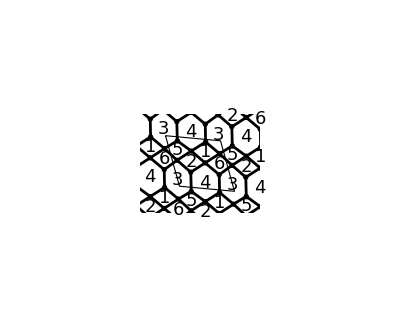

```mathematica
BraneTilingGraph[WPdP3cAFromDef1]
```

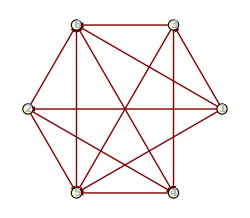
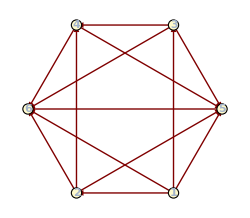

X_1[1,6]·X_1[6,5]·X_1[5,1] 1-a+X_1[4,5]·X_1[5,6]·X_1[6,4] 1-a+X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,1] 1-a+X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] 1-a+X_1[2,5]·X_1[5,6]·X_1[6,2] -1+a+X_1[3,6]·X_1[6,5]·X_1[5,3] -1+a+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1] -1+a+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1] -1+a

```mathematica
Row@{
QuiverGraph[WPdP3cPhaseA],
(WPdP3cAFromDef1//ReplaceAll[{Subscript[X, 1][1,2]->Subscript[X, 1][3,4],Subscript[X, 1][1,3]->Subscript[X, 1][3,6],Subscript[X, 1][2,4]->Subscript[X, 1][4,5],Subscript[X, 1][2,5]->Subscript[X, 1][4,2],Subscript[X, 1][3,2]->Subscript[X, 1][6,4],Subscript[X, 1][3,4]->Subscript[X, 1][6,5],Subscript[X, 1][3,5]->Subscript[X, 1][6,2],Subscript[X, 1][4,1]->Subscript[X, 1][5,3],Subscript[X, 1][4,3]->Subscript[X, 1][5,6],Subscript[X, 1][4,6]->Subscript[X, 1][5,1],Subscript[X, 1][5,4]->Subscript[X, 1][2,5],Subscript[X, 1][5,6]->Subscript[X, 1][2,1],Subscript[X, 1][6,1]->Subscript[X, 1][1,3],Subscript[X, 1][6,3]->Subscript[X, 1][1,6]}])//QuiverGraph[{5,3,4,6,2,1},#]&
}
a WPdP3cPhaseA+(WPdP3cAFromDef1//ReplaceAll[{Subscript[X, 1][1,2]->Subscript[X, 1][3,4],Subscript[X, 1][1,3]->Subscript[X, 1][3,6],Subscript[X, 1][2,4]->Subscript[X, 1][4,5],Subscript[X, 1][2,5]->Subscript[X, 1][4,2],Subscript[X, 1][3,2]->Subscript[X, 1][6,4],Subscript[X, 1][3,4]->Subscript[X, 1][6,5],Subscript[X, 1][3,5]->Subscript[X, 1][6,2],Subscript[X, 1][4,1]->Subscript[X, 1][5,3],Subscript[X, 1][4,3]->Subscript[X, 1][5,6],Subscript[X, 1][4,6]->Subscript[X, 1][5,1],Subscript[X, 1][5,4]->Subscript[X, 1][2,5],Subscript[X, 1][5,6]->Subscript[X, 1][2,1],Subscript[X, 1][6,1]->Subscript[X, 1][1,3],Subscript[X, 1][6,3]->Subscript[X, 1][1,6]}])//Expand@Collect[Expand@Simplify@#,c_CenterDot,Highlighted]&
```

### PdP_(3c) (a) ⟹ PdP_(3b) (a)

#### Deformation 1: (1→6→2→1) – (3→4→5→3)

```mathematica
PdP3cPhaseADef1η=Subscript[X, 1][1,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,1];
WPdP3cPhaseADef1=WPdP3cPhaseA+μ (Subscript[X, 1][1,6]·Subscript[X, 1][6,2]·Subscript[X, 1][2,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3])
```

-(X_1[1,6]·X_1[6,5]·X_1[5,1])+X_1[2,5]·X_1[5,6]·X_1[6,2]+μ (X_1[1,6]·X_1[6,2]·X_1[2,1]-X_1[3,4]·X_1[4,5]·X_1[5,3])+X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]-X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,1]+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]

```mathematica
RedefChoice3={Subscript[β, 1][1,6]->Subscript[β, 1][5,3],Subscript[β, 1][4,5]->Subscript[β, 1][6,2],Subscript[β, 1][6,2]->-1/μ,Subscript[β, 1][6,2]->-1/μ,Subscript[β, 1][5,3]->1/μ,Subscript[α, 1][4,5]->1/μ,Subscript[α, 1][6,2]->1/μ,Subscript[α, 1][5,3]->-1/μ,Subscript[α, 1][1,6]->-1/μ};
RedefRules3=FieldRedefinition[{Subscript[X, 1][1,6], Subscript[X, 1][6,2], Subscript[X, 1][4,5], Subscript[X, 1][5,3]},QuiverFromFields@WPdP3cPhaseA,2]//.RedefChoice3;
RedefRules3Mass={Subscript[X, 1][5,1]->μ Subscript[X, 1][5,1],Subscript[X, 1][5,3]->μ Subscript[X, 1][5,3],Subscript[X, 1][6,2]->μ Subscript[X, 1][6,2],Subscript[X, 1][6,4]->μ Subscript[X, 1][6,4]};
RedefRules3//Column
RedefRules3Mass//Column
```

X_1[1,6]→(X_1[1,3]·X_1[3,6])/μ-X_1[1,6]/μ
X_1[6,2]→-(X_1[6,4]·X_1[4,2])/μ+X_1[6,2]/μ
X_1[4,5]→-(X_1[4,2]·X_1[2,5])/μ+X_1[4,5]/μ
X_1[5,3]→(X_1[5,1]·X_1[1,3])/μ-X_1[5,3]/μ

X_1[5,1]→μ X_1[5,1]
X_1[5,3]→μ X_1[5,3]
X_1[6,2]→μ X_1[6,2]
X_1[6,4]→μ X_1[6,4]

```mathematica
DG[FieldCases[RedefRules3]/.RedefRules3,{FieldCases[RedefRules3]}]/.{Untrace->1}//Det
```

1/μ^4

```mathematica
WPdP3cPhaseADef1/.RedefRules3/.RedefRules3Mass//FTermsTable
```

X_1[1,3] | X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] -1+X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,1] 1 | 0 | 2
X_1[1,6] | X_1[6,2]·X_1[2,1] -1+X_1[6,5]·X_1[5,1] 1 | 0 | 2
X_1[2,1] | X_1[1,6]·X_1[6,2] -1+X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[2,5] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,6]·X_1[6,2] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_1[5,1]·X_1[1,3] -1+X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,6] | X_1[6,5]·X_1[5,3] -1+X_1[6,4]·X_1[4,2]·X_1[2,1]·X_1[1,3] 1 | 0 | 2
X_1[4,2] | X_1[2,5]·X_1[5,1]·X_1[1,3]·X_1[3,4] -1+X_1[2,1]·X_1[1,3]·X_1[3,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[1,6]·X_1[6,5] 1 | 0 | 2
X_1[5,3] | X_1[3,6]·X_1[6,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,2]·X_1[2,5] 1 | 0 | 2
X_1[6,2] | X_1[2,1]·X_1[1,6] -1+X_1[2,5]·X_1[5,6] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_1[2,1]·X_1[1,3]·X_1[3,6] 1 | 0 | 2
X_1[6,5] | X_1[5,3]·X_1[3,6] -1+X_1[5,1]·X_1[1,6] 1 | 0 | 2

```mathematica
WPdP3bAFromDef1=Simplify[WPdP3cPhaseADef1/.RedefRules3/.RedefRules3Mass]
```

-(X_1[1,6]·X_1[6,2]·X_1[2,1])+X_1[1,6]·X_1[6,5]·X_1[5,1]+X_1[2,5]·X_1[5,6]·X_1[6,2]+X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[3,6]·X_1[6,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]+X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]

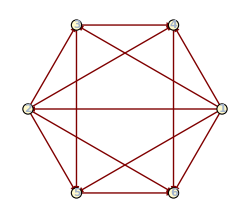
-Graphics--Graphics-

X_1[1,2]·X_1[2,5]·X_1[5,1] 1-a+X_1[1,3]·X_1[3,2]·X_1[2,1] 1-a+X_1[1,4]·X_1[4,6]·X_1[6,1] 1-a+X_1[2,6]·X_1[6,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] 1-a+X_1[1,2]·X_1[2,6]·X_1[6,1] -1+a+X_1[1,4]·X_1[4,2]·X_1[2,1] -1+a+X_1[2,5]·X_1[5,3]·X_1[3,2] -1+a+X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,1] -1+a

```mathematica
Row[{
QuiverGraph[{1,4,3,2,5,6},QuiverFromFields[WPdP3bPhaseA]],
WPdP3bAFromDef1/.ChangeGroupIndices[{3,5,4,6,1,2}]//QuiverGraph[{1,4,3,2,5,6},#]&
}]
a WPdP3bPhaseA+(WPdP3bAFromDef1/.ChangeGroupIndices[{3,5,4,6,1,2}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

### PdP_(3c) (a) ⟹ Non-toric (3-term F-terms model)

#### Deformation 2: (5→6→5) – (1→3→4→2→1)

```mathematica
δWPdP3cPhaseADef2=m (Subscript[X, 1][5,6]·Subscript[X, 1][6,5]-Subscript[X, 1][1,3]·Subscript[X, 1][3,4]·Subscript[X, 1][4,2]·Subscript[X, 1][2,1]);
WPdP3cPhaseADef2=WPdP3cPhaseA+δWPdP3cPhaseADef2;
```

```mathematica
massiveFieldsFrom[WPdP3cPhaseADef2];
WPdP3cPhaseADef2Min=WPdP3cPhaseADef2/.Last@Solve[DG[WPdP3cPhaseADef2,{%}]==0,%]//Expand
```

-m X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]-X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,1]+(X_1[1,6]·X_1[6,2]·X_1[2,5]·X_1[5,1])/m+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]-(X_1[1,6]·X_1[6,4]·X_1[4,5]·X_1[5,1])/m+(X_1[2,5]·X_1[5,1]·X_1[1,6]·X_1[6,2])/m-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]-(X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,2])/m-(X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,3])/m+(X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3])/m-(X_1[4,5]·X_1[5,1]·X_1[1,6]·X_1[6,4])/m+(X_1[4,5]·X_1[5,3]·X_1[3,6]·X_1[6,4])/m-(X_1[5,1]·X_1[1,6]·X_1[6,2]·X_1[2,5])/m+(X_1[5,1]·X_1[1,6]·X_1[6,4]·X_1[4,5])/m+(X_1[5,3]·X_1[3,6]·X_1[6,2]·X_1[2,5])/m-(X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5])/m

```mathematica
FTermsTable[WPdP3cPhaseADef2Min]
```

X_1[1,3] | X_1[3,6]·X_1[6,2]·X_1[2,1] -1+X_1[3,4]·X_1[4,5]·X_1[5,1] 1+X_1[3,4]·X_1[4,2]·X_1[2,1] -m | -m | 2+Abs[m]
X_1[1,6] | X_1[6,4]·X_1[4,2]·X_1[2,1] 1+X_1[6,4]·X_1[4,5]·X_1[5,1] -1/m+X_1[6,2]·X_1[2,5]·X_1[5,1] 1/m | 1 | 1+2/Abs[m]
X_1[2,1] | X_1[1,3]·X_1[3,6]·X_1[6,2] -1+X_1[1,6]·X_1[6,4]·X_1[4,2] 1+X_1[1,3]·X_1[3,4]·X_1[4,2] -m | -m | 2+Abs[m]
X_1[2,5] | X_1[5,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,3]·X_1[3,6]·X_1[6,2] -1/m+X_1[5,1]·X_1[1,6]·X_1[6,2] 1/m | -1 | 1+2/Abs[m]
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_1[5,3] -1+X_1[4,5]·X_1[5,1]·X_1[1,3] 1+X_1[4,2]·X_1[2,1]·X_1[1,3] -m | -m | 2+Abs[m]
X_1[3,6] | X_1[6,2]·X_1[2,1]·X_1[1,3] -1+X_1[6,2]·X_1[2,5]·X_1[5,3] -1/m+X_1[6,4]·X_1[4,5]·X_1[5,3] 1/m | -1 | 1+2/Abs[m]
X_1[4,2] | X_1[2,5]·X_1[5,3]·X_1[3,4] -1+X_1[2,1]·X_1[1,6]·X_1[6,4] 1+X_1[2,1]·X_1[1,3]·X_1[3,4] -m | -m | 2+Abs[m]
X_1[4,5] | X_1[5,1]·X_1[1,3]·X_1[3,4] 1+X_1[5,1]·X_1[1,6]·X_1[6,4] -1/m+X_1[5,3]·X_1[3,6]·X_1[6,4] 1/m | 1 | 1+2/Abs[m]
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,5] 1+X_1[1,6]·X_1[6,4]·X_1[4,5] -1/m+X_1[1,6]·X_1[6,2]·X_1[2,5] 1/m | 1 | 1+2/Abs[m]
X_1[5,3] | X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[3,6]·X_1[6,2]·X_1[2,5] -1/m+X_1[3,6]·X_1[6,4]·X_1[4,5] 1/m | -1 | 1+2/Abs[m]
X_1[6,2] | X_1[2,1]·X_1[1,3]·X_1[3,6] -1+X_1[2,5]·X_1[5,3]·X_1[3,6] -1/m+X_1[2,5]·X_1[5,1]·X_1[1,6] 1/m | -1 | 1+2/Abs[m]
X_1[6,4] | X_1[4,2]·X_1[2,1]·X_1[1,6] 1+X_1[4,5]·X_1[5,1]·X_1[1,6] -1/m+X_1[4,5]·X_1[5,3]·X_1[3,6] 1/m | 1 | 1+2/Abs[m]

### PdP_(3c) (b) ⟹ PdP_(3b) (b)

#### Deformation 1: (2→6→2) – (1→5→3→1) = PdP_(3b) (b)

```mathematica
δWPdP3cPhaseBDef1=m (Subscript[X, 1][2,6]·Subscript[X, 1][6,2]-Subscript[X, 1][1,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1] );
WPdP3cPhaseBDef1=WPdP3cPhaseB+δWPdP3cPhaseBDef1;
```

```mathematica
WPdP3cPhaseBDef1Min=WPdP3cPhaseBDef1//IntegrateOutMassTerms//Expand
```

X_1[1,2]·X_1[2,3]·X_1[3,1]-m X_1[1,5]·X_1[5,3]·X_1[3,1]-X_1[1,5]·X_2[5,3]·X_1[3,1]+X_1[3,4]·X_1[4,5]·X_2[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]-(X_1[1,2]·X_1[2,3]·X_1[3,6]·X_1[6,1])/m+(X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1])/m+X_1[1,5]·X_1[5,3]·X_1[3,6]·X_1[6,1]+(X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2])/m-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]-(X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2])/m

```mathematica
RedefChoice4={Subscript[β, 1][3,1]->1/m,Subscript[α, 1][3,1]->-1/m,Subscript[β, 1][4,5]->-1/m,Subscript[α, 1][4,5]->1/m,Subscript[β, 1][5,3]->-1/m,Subscript[α, 1][5,3]->1/m};
RedefRules4=FieldRedefinition[{Subscript[X, 1][3,1],Subscript[X, 1][5,3],Subscript[X, 1][4,5]},QuiverFromFields[WPdP3cPhaseB],2]//.RedefChoice4;
RedefRules4Mass={Subscript[X, 1][3,1]->m Subscript[X, 1][3,1],Subscript[X, 1][4,2]->m Subscript[X, 1][4,2],Subscript[X, 2][5,3]->m Subscript[X, 2][5,3],Subscript[X, 1][5,6]->m Subscript[X, 1][5,6]};
RedefRules4//Column
RedefRules4Mass//Column
```

X_1[3,1]→(X_1[3,6]·X_1[6,1])/m-X_1[3,1]/m
X_1[5,3]→X_1[5,3]/m-X_2[5,3]/m
X_1[4,5]→-(X_1[4,2]·X_1[2,5])/m+X_1[4,5]/m

X_1[3,1]→m X_1[3,1]
X_1[4,2]→m X_1[4,2]
X_2[5,3]→m X_2[5,3]
X_1[5,6]→m X_1[5,6]

```mathematica
DG[FieldCases[RedefRules4]/.RedefRules4,{FieldCases[RedefRules4]}]/.{Untrace->1}//Det
```

-1/m^3

```mathematica
WPdP3cPhaseBDef1Min/.RedefRules4/.RedefRules4Mass//FTermsTable
```

X_1[1,2] | X_1[2,3]·X_1[3,1] -1+X_1[2,5]·X_1[5,6]·X_1[6,1] 1 | 0 | 2
X_1[1,5] | X_2[5,3]·X_1[3,6]·X_1[6,1] -1+X_1[5,3]·X_1[3,1] 1 | 0 | 2
X_1[2,3] | X_1[3,1]·X_1[1,2] -1+X_1[3,6]·X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[2,5] | X_1[5,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,6]·X_1[6,1]·X_1[1,2] 1 | 0 | 2
X_1[3,1] | X_1[1,2]·X_1[2,3] -1+X_1[1,5]·X_1[5,3] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_1[5,3] -1+X_1[4,5]·X_2[5,3] 1 | 0 | 2
X_1[3,6] | X_1[6,1]·X_1[1,5]·X_2[5,3] -1+X_1[6,4]·X_1[4,2]·X_1[2,3] 1 | 0 | 2
X_1[4,2] | X_1[2,5]·X_1[5,3]·X_1[3,4] -1+X_1[2,3]·X_1[3,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_2[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,3] | X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[3,1]·X_1[1,5] 1 | 0 | 2
X_2[5,3] | X_1[3,6]·X_1[6,1]·X_1[1,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,1]·X_1[1,2]·X_1[2,5] 1 | 0 | 2
X_1[6,1] | X_1[1,5]·X_2[5,3]·X_1[3,6] -1+X_1[1,2]·X_1[2,5]·X_1[5,6] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_1[2,3]·X_1[3,6] 1 | 0 | 2

```mathematica
WPdP3bBFromDef1=Simplify[WPdP3cPhaseBDef1Min/.RedefRules4/.RedefRules4Mass]
```

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,5]·X_1[5,3]·X_1[3,1]+X_1[3,4]·X_1[4,5]·X_2[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]-X_1[1,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]+X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]

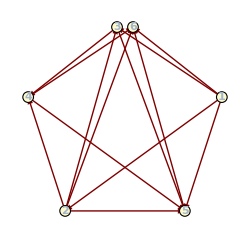
-Graphics--Graphics-

X_1[1,3]·X_1[3,2]·X_1[2,1] -1-a+X_1[4,5]·X_1[5,6]·X_1[6,4] -1-a+X_1[1,6]·X_1[6,2]·X_2[2,5]·X_1[5,1] -1-a+X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] -1-a+X_1[2,5]·X_1[5,6]·X_1[6,2] 1+a+X_1[3,2]·X_2[2,5]·X_1[5,3] 1+a+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1] 1+a+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1] 1+a

```mathematica
Row[{
QuiverGraph[{1,{6,3},4,2,5},QuiverFromFields[WPdP3bPhaseB]],
WPdP3bBFromDef1/.ChangeGroupIndices[{6,4,5,3,2,1}]//QuiverGraph[{1,{6,3},4,2,5},QuiverFromFields@#]&
}]
a WPdP3bPhaseB+(WPdP3bBFromDef1/.ChangeGroupIndices[{6,4,5,3,2,1}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

```mathematica
WPdP3bBFromDef1+1/m Total@ZigZagOperator[WPdP3bBFromDef1,Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,1]]//Expand
Expand[WPdP3cPhaseBDef1Min/.RedefRules4[[1]]/.{Subscript[X, 1][2,3]->m Subscript[X, 1][2,3],Subscript[X, 1][6,1]->m Subscript[X, 1][6,1]}]
%==%%
```

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,5]·X_1[5,3]·X_1[3,1]+(X_1[1,5]·X_2[5,3]·X_1[3,1])/m+X_1[3,4]·X_1[4,5]·X_2[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]-X_1[1,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]+X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]-(X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2])/m

-(X_1[1,2]·X_1[2,3]·X_1[3,1])+X_1[1,5]·X_1[5,3]·X_1[3,1]+(X_1[1,5]·X_2[5,3]·X_1[3,1])/m+X_1[3,4]·X_1[4,5]·X_2[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]+X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]-X_1[1,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]+X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]-X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]-(X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2])/m

True

```mathematica
Total@ZigZagOperator[WPdP3bBFromDef1,Subscript[X, 1][1,2]·Subscript[X, 1][2,3]·Subscript[X, 1][3,6]·Subscript[X, 1][6,1]]
```

X_1[1,5]·X_2[5,3]·X_1[3,1]-X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2]

### PdP_(3c) (b) == PdP_(3c) (b)

#### Deformation 2: (1→5→3→1) – (3→4→5→3)

```mathematica
δWPdP3cPhaseBDef2=m (Subscript[X, 1][1,5]·Subscript[X, 1][5,3]·Subscript[X, 1][3,1] -Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]);
WPdP3cPhaseBDef2=WPdP3cPhaseB+δWPdP3cPhaseBDef2;
```

```mathematica
RedefChoice5={Subscript[γ, 1][2,6]->-1/m-Subscript[β, 1][2,6],Subscript[β, 1][5,3]->1/m,Subscript[β, 1][3,1]->-1/m,Subscript[γ, 1][6,2]->-1/m-Subscript[β, 1][2,6],Subscript[α, 1][3,1]->1/m,Subscript[β, 1][6,2]->Subscript[β, 1][2,6],Subscript[β, 1][4,5]->-1/m,Subscript[α, 1][4,5]->1/m,Subscript[α, 1][6,2]->1/m,Subscript[α, 1][2,6]->1/m,Subscript[α, 1][5,3]->-1/m};
RedefRules5=FieldRedefinition[{Subscript[X, 1][6,2],Subscript[X, 1][2,6],Subscript[X, 1][4,5],Subscript[X, 1][3,1],Subscript[X, 1][5,3]},QuiverFromFields[WPdP3cPhaseB],2]//.RedefChoice5;
RedefRules5Mass={Subscript[X, 1][3,1]->m Subscript[X, 1][3,1],Subscript[X, 1][4,2]->m Subscript[X, 1][4,2],Subscript[X, 1][4,5]->m Subscript[X, 1][4,5],Subscript[X, 1][6,1]->m Subscript[X, 1][6,1],Subscript[X, 1][6,2]->m Subscript[X, 1][6,2]};
RedefRules5//Column
RedefRules5Mass//Column
```

X_1[6,2]→X_1[6,1]·X_1[1,2] (-1/m-β_1[2,6])+X_1[6,4]·X_1[4,2] β_1[2,6]+X_1[6,2]/m
X_1[2,6]→X_1[2,5]·X_1[5,6] (-1/m-β_1[2,6])+X_1[2,3]·X_1[3,6] β_1[2,6]+X_1[2,6]/m
X_1[4,5]→-(X_1[4,2]·X_1[2,5])/m+X_1[4,5]/m
X_1[3,1]→-(X_1[3,6]·X_1[6,1])/m+X_1[3,1]/m
X_1[5,3]→-X_1[5,3]/m+X_2[5,3]/m

X_1[3,1]→m X_1[3,1]
X_1[4,2]→m X_1[4,2]
X_1[4,5]→m X_1[4,5]
X_1[6,1]→m X_1[6,1]
X_1[6,2]→m X_1[6,2]

```mathematica
DG[FieldCases[RedefRules5]/.RedefRules5,{FieldCases[RedefRules5]}]/.{Untrace->1}//Det
```

-1/m^5

```mathematica
WPdP3cPhaseBDef2/.RedefRules5/.RedefRules5Mass//FTermsTable
```

X_1[1,2] | X_1[2,6]·X_1[6,1] -1+X_1[2,3]·X_1[3,1] 1 | 0 | 2
X_1[1,5] | X_1[5,3]·X_1[3,1] -1+X_2[5,3]·X_1[3,6]·X_1[6,1] 1 | 0 | 2
X_1[2,3] | X_1[3,6]·X_1[6,2] -1+X_1[3,1]·X_1[1,2] 1 | 0 | 2
X_1[2,5] | X_2[5,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,6]·X_1[6,2] 1 | 0 | 2
X_1[2,6] | X_1[6,1]·X_1[1,2] -1+X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[3,1] | X_1[1,5]·X_1[5,3] -1+X_1[1,2]·X_1[2,3] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_2[5,3] -1+X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[3,6] | X_1[6,2]·X_1[2,3] -1+X_1[6,1]·X_1[1,5]·X_2[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,5]·X_2[5,3]·X_1[3,4] -1+X_1[2,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,3] | X_1[3,1]·X_1[1,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_2[5,3] | X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[3,6]·X_1[6,1]·X_1[1,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,2]·X_1[2,5] 1 | 0 | 2
X_1[6,1] | X_1[1,2]·X_1[2,6] -1+X_1[1,5]·X_2[5,3]·X_1[3,6] 1 | 0 | 2
X_1[6,2] | X_1[2,3]·X_1[3,6] -1+X_1[2,5]·X_1[5,6] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_1[2,6] 1 | 0 | 2

```mathematica
WPdP3cBFromDef2=Simplify[WPdP3cPhaseBDef2/.RedefRules5/.RedefRules5Mass];
```

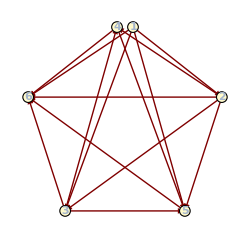
-Graphics--Graphics-

X_1[1,2]·X_1[2,6]·X_1[6,1] -1-a+X_1[1,5]·X_2[5,3]·X_1[3,1] -1-a+X_1[2,3]·X_1[3,6]·X_1[6,2] -1-a+X_1[4,5]·X_1[5,6]·X_1[6,4] -1-a+X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2] -1-a+X_1[1,2]·X_1[2,3]·X_1[3,1] 1+a+X_1[2,5]·X_1[5,6]·X_1[6,2] 1+a+X_1[2,6]·X_1[6,4]·X_1[4,2] 1+a+X_1[3,4]·X_1[4,5]·X_2[5,3] 1+a+X_1[1,5]·X_1[5,3]·X_1[3,6]·X_1[6,1] 1+a

```mathematica
Row[{
QuiverGraph[{2,{1,4},6,3,5},QuiverFromFields[WPdP3cPhaseB],ImageSize->250],
WPdP3cPhaseBDef2/.RedefRules5/.RedefRules5Mass//QuiverGraph[{2,{1,4},6,3,5},#,ImageSize->250]&
}]
a WPdP3cPhaseB+(WPdP3cBFromDef2/.{Subscript[X, 2][5,3]->Subscript[X, 1][5,3],Subscript[X, 1][5,3]->Subscript[X, 2][5,3]})//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

### PdP_(3b) (a) ⟹ dP_3 (a)

#### Deformation 1: (1→2→1) – (3→4→6→5→3)

```mathematica
δWPdP3bPhaseADef1=m (Subscript[X, 1][1,2]·Subscript[X, 1][2,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,6]·Subscript[X, 1][6,5]·Subscript[X, 1][5,3]);
WPdP3bPhaseADef1=WPdP3bPhaseA+δWPdP3bPhaseADef1;
```

```mathematica
massiveFieldsFrom[WPdP3bPhaseADef1]
WPdP3bPhaseADef1Min=WPdP3bPhaseADef1/.Last@Solve[DG[WPdP3bPhaseADef1,{%}]==0,%]//Expand
```

{X_1[1,2],X_1[2,1]}

-(X_1[1,4]·X_1[4,6]·X_1[6,1])+X_1[2,5]·X_1[5,3]·X_1[3,2]-(X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1])/m+(X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1])/m+(X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1])/m-(X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1])/m-m X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,3]+X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,1]-X_1[2,6]·X_1[6,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]

```mathematica
Clear[RedefChoice6,RedefRules6]
RedefChoice6={Subscript[β, 1][5,3]->1/m,Subscript[β, 1][4,6]->-1/m,Subscript[α, 1][4,6]->1/m,Subscript[α, 1][5,3]->-1/m};
RedefRules6=FieldRedefinition[{Subscript[X, 1][5,3],Subscript[X, 1][4,6]},QuiverFromFields[WPdP3bPhaseA],2]//.RedefChoice6;
RedefRules6Mass={Subscript[X, 1][5,1]->m Subscript[X, 1][5,1],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][6,1]->m Subscript[X, 1][6,1]};
RedefRules6//Column
RedefRules6Mass//Column
```

X_1[5,3]→(X_1[5,1]·X_1[1,3])/m-X_1[5,3]/m
X_1[4,6]→-(X_1[4,2]·X_1[2,6])/m+X_1[4,6]/m

X_1[5,1]→m X_1[5,1]
X_1[5,3]→m X_1[5,3]
X_1[6,1]→m X_1[6,1]

```mathematica
DG[FieldCases[RedefRules6]/.RedefRules6,{FieldCases[RedefRules6]}]/.{Untrace->1}//Det
```

-1/m^2

```mathematica
WPdP3bPhaseADef1Min/.RedefRules6/.RedefRules6Mass//FTermsTable
```

X_1[1,3] | X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1] -1+X_1[3,2]·X_1[2,6]·X_1[6,1] 1 | 0 | 2
X_1[1,4] | X_1[4,6]·X_1[6,1] -1+X_1[4,2]·X_1[2,5]·X_1[5,1] 1 | 0 | 2
X_1[2,5] | X_1[5,3]·X_1[3,2] -1+X_1[5,1]·X_1[1,4]·X_1[4,2] 1 | 0 | 2
X_1[2,6] | X_1[6,5]·X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2] -1+X_1[6,1]·X_1[1,3]·X_1[3,2] 1 | 0 | 2
X_1[3,2] | X_1[2,5]·X_1[5,3] -1+X_1[2,6]·X_1[6,1]·X_1[1,3] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]·X_1[1,3] -1+X_1[4,6]·X_1[6,5]·X_1[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,6]·X_1[6,5]·X_1[5,1]·X_1[1,3]·X_1[3,4] -1+X_1[2,5]·X_1[5,1]·X_1[1,4] 1 | 0 | 2
X_1[4,6] | X_1[6,1]·X_1[1,4] -1+X_1[6,5]·X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,5] -1+X_1[1,4]·X_1[4,2]·X_1[2,5] 1 | 0 | 2
X_1[5,3] | X_1[3,2]·X_1[2,5] -1+X_1[3,4]·X_1[4,6]·X_1[6,5] 1 | 0 | 2
X_1[6,1] | X_1[1,4]·X_1[4,6] -1+X_1[1,3]·X_1[3,2]·X_1[2,6] 1 | 0 | 2
X_1[6,5] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6] -1+X_1[5,3]·X_1[3,4]·X_1[4,6] 1 | 0 | 2

```mathematica
WdP3AFromDef1=Simplify[WPdP3bPhaseADef1Min/.RedefRules6/.RedefRules6Mass]
```

-(X_1[1,4]·X_1[4,6]·X_1[6,1])-X_1[2,5]·X_1[5,3]·X_1[3,2]+X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]+X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]+X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,3]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]

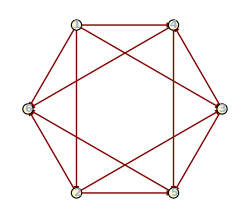
-Graphics--Graphics-

X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1] 1-a+X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1] 1-a+X_1[2,6]·X_1[6,4]·X_1[4,3]·X_1[3,2] 1-a+X_1[1,3]·X_1[3,2]·X_1[2,1] -1+a+X_1[4,5]·X_1[5,6]·X_1[6,4] -1+a+X_1[1,4]·X_1[4,3]·X_1[3,5]·X_1[5,2]·X_1[2,6]·X_1[6,1] -1+a

```mathematica
Row[{
QuiverGraph[{3,4,1,6,2,5},QuiverFromFields[WdP3PhaseA]],
WdP3AFromDef1/.ChangeGroupIndices[{6,3,1,4,2,5}]//QuiverGraph[{3,4,1,6,2,5},#]&
}]
a WdP3PhaseA+(WdP3AFromDef1/.ChangeGroupIndices[{6,3,1,4,2,5}])//Expand@Collect[Expand@Simplify@#,_CenterDot,Highlighted]&
```

### PdP_(3b) (b) ⟹ dP_3 (b)

#### Deformation 1: (1→6→2→1) – (3→4→5→3)

```mathematica
δWPdP3bPhaseBDef1=m (Subscript[X, 1][1,6]· Subscript[X, 1][6,2]·Subscript[X, 1][2,1]-Subscript[X, 1][3,4]·Subscript[X, 1][4,5]·Subscript[X, 1][5,3]);
WPdP3bPhaseBDef1=WPdP3bPhaseB+δWPdP3bPhaseBDef1;
```

```mathematica
RedefChoice7={Subscript[β, 1][5,3]->1/m,Subscript[γ, 1][2,1]->1/m,Subscript[β, 1][2,1]-> 0,Subscript[β, 1][6,2]->-1/m,Subscript[β, 1][4,5]->-1/m, Subscript[γ, 1][4,5]->0,Subscript[α, 1][4,5]->1/m,Subscript[α, 1][6,2]->1/m,Subscript[α, 1][5,3]->-1/m,Subscript[α, 1][2,1]->-1/m};
RedefRules7=FieldRedefinition[{Subscript[X, 1][4,5],Subscript[X, 1][5,3],Subscript[X, 1][2,1],Subscript[X, 1][6,2]},QuiverFromFields[WPdP3bPhaseB],2]//.RedefChoice7;
RedefRules7Mass={Subscript[X, 1][2,1]->m Subscript[X, 1][2,1],Subscript[X, 1][5,1]->m Subscript[X, 1][5,1],Subscript[X, 1][5,3]->m Subscript[X, 1][5,3],Subscript[X, 1][5,6]->m Subscript[X, 1][5,6]};
RedefRules7//Column
RedefRules7Mass//Column
```

X_1[4,5]→-(X_1[4,2]·X_1[2,5])/m+X_1[4,5]/m
X_1[5,3]→(X_1[5,1]·X_1[1,3])/m-X_1[5,3]/m
X_1[2,1]→(X_2[2,5]·X_1[5,1])/m-X_1[2,1]/m
X_1[6,2]→-(X_1[6,4]·X_1[4,2])/m+X_1[6,2]/m

X_1[2,1]→m X_1[2,1]
X_1[5,1]→m X_1[5,1]
X_1[5,3]→m X_1[5,3]
X_1[5,6]→m X_1[5,6]

```mathematica
DG[FieldCases[RedefRules7]/.RedefRules7,{FieldCases[RedefRules7]}]/.{Untrace->1}//Det
```

1/m^4

```mathematica
WPdP3bPhaseBDef1/.RedefRules7/.RedefRules7Mass//FTermsTable
```

X_1[1,3] | X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1] -1+X_1[3,2]·X_1[2,1] 1 | 0 | 2
X_1[1,6] | X_1[6,2]·X_1[2,1] -1+X_1[6,4]·X_1[4,2]·X_2[2,5]·X_1[5,1] 1 | 0 | 2
X_1[2,1] | X_1[1,6]·X_1[6,2] -1+X_1[1,3]·X_1[3,2] 1 | 0 | 2
X_1[2,5] | X_1[5,1]·X_1[1,3]·X_1[3,4]·X_1[4,2] -1+X_1[5,6]·X_1[6,2] 1 | 0 | 2
X_2[2,5] | X_1[5,3]·X_1[3,2] -1+X_1[5,1]·X_1[1,6]·X_1[6,4]·X_1[4,2] 1 | 0 | 2
X_1[3,2] | X_2[2,5]·X_1[5,3] -1+X_1[2,1]·X_1[1,3] 1 | 0 | 2
X_1[3,4] | X_1[4,2]·X_1[2,5]·X_1[5,1]·X_1[1,3] -1+X_1[4,5]·X_1[5,3] 1 | 0 | 2
X_1[4,2] | X_1[2,5]·X_1[5,1]·X_1[1,3]·X_1[3,4] -1+X_2[2,5]·X_1[5,1]·X_1[1,6]·X_1[6,4] 1 | 0 | 2
X_1[4,5] | X_1[5,6]·X_1[6,4] -1+X_1[5,3]·X_1[3,4] 1 | 0 | 2
X_1[5,1] | X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5] -1+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_2[2,5] 1 | 0 | 2
X_1[5,3] | X_1[3,2]·X_2[2,5] -1+X_1[3,4]·X_1[4,5] 1 | 0 | 2
X_1[5,6] | X_1[6,4]·X_1[4,5] -1+X_1[6,2]·X_1[2,5] 1 | 0 | 2
X_1[6,2] | X_1[2,1]·X_1[1,6] -1+X_1[2,5]·X_1[5,6] 1 | 0 | 2
X_1[6,4] | X_1[4,5]·X_1[5,6] -1+X_1[4,2]·X_2[2,5]·X_1[5,1]·X_1[1,6] 1 | 0 | 2

```mathematica
WdP3BFromDef1=Simplify[WPdP3bPhaseBDef1/.RedefRules7/.RedefRules7Mass]
```

X_1[1,3]·X_1[3,2]·X_1[2,1]-X_1[1,6]·X_1[6,2]·X_1[2,1]+X_1[2,5]·X_1[5,6]·X_1[6,2]-X_1[3,2]·X_2[2,5]·X_1[5,3]+X_1[3,4]·X_1[4,5]·X_1[5,3]-X_1[4,5]·X_1[5,6]·X_1[6,4]-X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]+X_1[1,6]·X_1[6,4]·X_1[4,2]·X_2[2,5]·X_1[5,1]

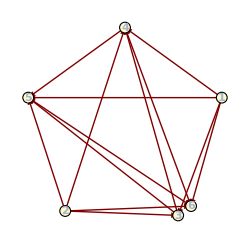
-Graphics--Graphics-

X_1[1,5]·X_1[5,6]·X_1[6,1] -1-a+X_1[2,6]·X_1[6,4]·X_1[4,2] -1-a+X_1[3,4]·X_1[4,5]·X_1[5,3] -1-a+X_1[1,4]·X_2[4,5]·X_1[5,2]·X_1[2,3]·X_1[3,1] -1-a+X_1[1,5]·X_1[5,3]·X_1[3,1] 1+a+X_1[2,3]·X_1[3,4]·X_1[4,2] 1+a+X_1[5,6]·X_1[6,4]·X_2[4,5] 1+a+X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,6]·X_1[6,1] 1+a

```mathematica
Row[{
QuiverGraph[Automatic,QuiverFromFields[WdP3PhaseB]],
WdP3BFromDef1/.ChangeGroupIndices[{2,4,3,1,5,6}]//QuiverGraph[Expand@#]&
}]
a WdP3PhaseB+(WdP3BFromDef1/.ChangeGroupIndices[{2,4,3,1,5,6}]/.{Subscript[X, 2][4,5]->Subscript[X, 1][4,5],Subscript[X, 1][4,5]->Subscript[X, 2][4,5]})//Expand@Collect[Expand@Simplify@#,c_CenterDot,Highlighted]&
```

### PdP_(3b) (c) ⟹ dP_3 (c)

#### Deformation 1: (3→5→3) – (1→6→2→1)

```mathematica
δWPdP3bPhaseCDef=m (Subscript[X, 1][3,5]·Subscript[X, 1][5,3]-Subscript[X, 1][1,6]·Subscript[X, 1][6,2]·Subscript[X, 1][2,1]);
WPdP3bPhaseCDef1=WPdP3bPhaseC+δWPdP3bPhaseCDef;
```

```mathematica
massiveFieldsFrom[WPdP3bPhaseCDef1]
WPdP3bPhaseCDef1Min=WPdP3bPhaseCDef1/.Last@Solve[DG[WPdP3bPhaseCDef1,{%}]==0,%]//Expand
```

{X_1[3,5],X_1[5,3]}

-(X_1[1,3]·X_1[3,2]·X_1[2,1])-m X_1[1,6]·X_1[6,2]·X_1[2,1]+X_1[1,6]·X_2[6,2]·X_1[2,1]+X_1[2,4]·X_1[4,3]·X_2[3,2]-X_1[2,4]·X_1[4,6]·X_2[6,2]-(X_1[1,3]·X_1[3,2]·X_2[2,5]·X_1[5,1])/m+(X_1[1,3]·X_2[3,2]·X_1[2,5]·X_1[5,1])/m-X_1[1,6]·X_1[6,2]·X_2[2,5]·X_1[5,1]+(X_1[2,5]·X_1[5,1]·X_1[1,3]·X_2[3,2])/m-(X_1[2,5]·X_1[5,4]·X_1[4,3]·X_2[3,2])/m+X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,2]+(X_1[3,2]·X_2[2,5]·X_1[5,4]·X_1[4,3])/m-(X_2[3,2]·X_1[2,5]·X_1[5,1]·X_1[1,3])/m

```mathematica
Clear[RedefChoice8,RedefRules8]
RedefChoice8={Subscript[γ, 1][2,1]->-1/m,Subscript[β, 1][2,1]->0,Subscript[β, 1][6,2]->1/m,Subscript[β, 1][2,4]->1/m,Subscript[α, 1][2,1]->1/m,Subscript[α, 1][6,2]->-1/m,Subscript[γ, 1][2,4]->0,Subscript[α, 1][2,4]->-1/m};
RedefRules8=FieldRedefinition[{Subscript[X, 1][2,1],Subscript[X, 1][2,4],Subscript[X, 1][6,2]},QuiverFromFields[WPdP3bPhaseC],2]//.RedefChoice8;
RedefRules8Mass={Subscript[X, 1][3,2]->m Subscript[X, 1][3,2],Subscript[X, 1][6,2]->m Subscript[X, 1][6,2],Subscript[X, 2][3,2]->m Subscript[X, 2][3,2],Subscript[X, 2][6,2]->m Subscript[X, 2][6,2]};
RedefRules8//Column
RedefRules8Mass//Column
```

X_1[2,1]→-(X_2[2,5]·X_1[5,1])/m+X_1[2,1]/m
X_1[2,4]→(X_1[2,5]·X_1[5,4])/m-X_1[2,4]/m
X_1[6,2]→-X_1[6,2]/m+X_2[6,2]/m

X_1[3,2]→m X_1[3,2]
X_1[6,2]→m X_1[6,2]
X_2[3,2]→m X_2[3,2]
X_2[6,2]→m X_2[6,2]

```mathematica
DG[FieldCases[RedefRules8]/.RedefRules8,{FieldCases[RedefRules8]}]/.{Untrace->1}//Det
```

1/m^3

```mathematica
WPdP3bPhaseCDef1Min/.RedefRules8/.RedefRules8Mass//FTermsTable
```

X_1[1,3] | X_1[3,2]·X_1[2,1] -1+X_2[3,2]·X_1[2,5]·X_1[5,1] 1 | 0 | 2
X_1[1,6] | X_2[6,2]·X_2[2,5]·X_1[5,1] -1+X_1[6,2]·X_1[2,1] 1 | 0 | 2
X_1[2,1] | X_1[1,3]·X_1[3,2] -1+X_1[1,6]·X_1[6,2] 1 | 0 | 2
X_1[2,4] | X_1[4,3]·X_2[3,2] -1+X_1[4,6]·X_2[6,2] 1 | 0 | 2
X_1[2,5] | X_1[5,4]·X_1[4,6]·X_1[6,2] -1+X_1[5,1]·X_1[1,3]·X_2[3,2] 1 | 0 | 2
X_2[2,5] | X_1[5,1]·X_1[1,6]·X_2[6,2] -1+X_1[5,4]·X_1[4,3]·X_1[3,2] 1 | 0 | 2
X_1[3,2] | X_1[2,1]·X_1[1,3] -1+X_2[2,5]·X_1[5,4]·X_1[4,3] 1 | 0 | 2
X_2[3,2] | X_1[2,4]·X_1[4,3] -1+X_1[2,5]·X_1[5,1]·X_1[1,3] 1 | 0 | 2
X_1[4,3] | X_2[3,2]·X_1[2,4] -1+X_1[3,2]·X_2[2,5]·X_1[5,4] 1 | 0 | 2
X_1[4,6] | X_1[6,2]·X_1[2,5]·X_1[5,4] -1+X_2[6,2]·X_1[2,4] 1 | 0 | 2
X_1[5,1] | X_1[1,6]·X_2[6,2]·X_2[2,5] -1+X_1[1,3]·X_2[3,2]·X_1[2,5] 1 | 0 | 2
X_1[5,4] | X_1[4,6]·X_1[6,2]·X_1[2,5] -1+X_1[4,3]·X_1[3,2]·X_2[2,5] 1 | 0 | 2
X_1[6,2] | X_1[2,5]·X_1[5,4]·X_1[4,6] -1+X_1[2,1]·X_1[1,6] 1 | 0 | 2
X_2[6,2] | X_2[2,5]·X_1[5,1]·X_1[1,6] -1+X_1[2,4]·X_1[4,6] 1 | 0 | 2

```mathematica
WdP3CFromDef1=Simplify[WPdP3bPhaseCDef1Min/.RedefRules8/.RedefRules8Mass]
```

-(X_1[1,3]·X_1[3,2]·X_1[2,1])+X_1[1,6]·X_1[6,2]·X_1[2,1]-X_1[2,4]·X_1[4,3]·X_2[3,2]+X_1[2,4]·X_1[4,6]·X_2[6,2]+X_1[1,3]·X_2[3,2]·X_1[2,5]·X_1[5,1]-X_1[1,6]·X_2[6,2]·X_2[2,5]·X_1[5,1]-X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,2]+X_1[3,2]·X_2[2,5]·X_1[5,4]·X_1[4,3]

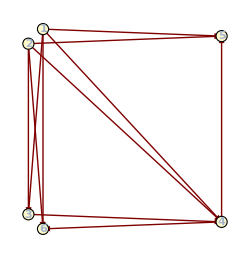
-Graphics--Graphics-

X_1[1,6]·X_2[6,4]·X_1[4,1] 1-a+X_1[2,6]·X_1[6,4]·X_1[4,2] 1-a+X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1] 1-a+X_1[2,3]·X_2[3,4]·X_2[4,5]·X_1[5,2] 1-a+X_1[1,3]·X_2[3,4]·X_1[4,1] -1+a+X_1[2,3]·X_1[3,4]·X_1[4,2] -1+a+X_1[1,6]·X_1[6,4]·X_2[4,5]·X_1[5,1] -1+a+X_1[2,6]·X_2[6,4]·X_1[4,5]·X_1[5,2] -1+a

```mathematica
Row@{
QuiverGraph[{5,{1,2},{3,6},4},QuiverFromFields[WdP3PhaseC]],
WdP3CFromDef1/.ChangeGroupIndices[{4->2,2->4}]//QuiverGraph[{5,{1,2},{3,6},4},#]&
}
a WdP3PhaseC+(WdP3CFromDef1/.ChangeGroupIndices[{4->2,2->4}]/.{Subscript[X, 2][3,4]->Subscript[X, 1][3,4],Subscript[X, 1][3,4]->Subscript[X, 2][3,4],Subscript[X, 1][6,4]->Subscript[X, 2][6,4],Subscript[X, 2][6,4]->Subscript[X, 1][6,4]})//Expand@Collect[Simplify@Expand@#,_CenterDot,Highlighted]&
```

## Mesonic branch

### Model 7: PdP_(3a) = ℂ^3/ℤ_6 (1,2,3)

```mathematica
PdP3aFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP3a,6];
```

```mathematica
PdP3aFieldGenRules=ReduceGenerators[W@PdP3a,Keys@PdP3aFieldGenRules0,PdP3aFieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP3aFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[3,4]·X_1[4,3]→A[1]
X_1[2,6]·X_1[6,2]→A[2]
X_1[1,5]·X_1[5,1]→A[3]
X_1[3,4]·X_1[4,6]·X_1[6,3]→B[3]
X_1[3,5]·X_1[5,6]·X_1[6,3]→B[2]
X_1[3,5]·X_1[5,4]·X_1[4,3]→B[3]
X_1[2,6]·X_1[6,3]·X_1[3,2]→B[3]
X_1[2,4]·X_1[4,6]·X_1[6,2]→B[3]
X_1[2,4]·X_1[4,3]·X_1[3,2]→B[3]
X_1[2,5]·X_1[5,6]·X_1[6,2]→B[3]
X_1[1,5]·X_1[5,6]·X_1[6,1]→B[3]
X_1[1,5]·X_1[5,4]·X_1[4,1]→B[3]
X_1[1,3]·X_1[3,4]·X_1[4,1]→B[3]
X_1[1,3]·X_1[3,5]·X_1[5,1]→B[3]
X_1[1,2]·X_1[2,6]·X_1[6,1]→B[3]
X_1[1,2]·X_1[2,4]·X_1[4,1]→B[13]
X_1[1,2]·X_1[2,5]·X_1[5,1]→B[3]
X_1[3,5]·X_1[5,4]·X_1[4,6]·X_1[6,3]→C[1]
X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2]→C[1]
X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2]→C[1]
X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,2]→C[4]
X_1[2,5]·X_1[5,4]·X_1[4,3]·X_1[3,2]→C[4]
X_1[1,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]→C[1]
X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1]→C[1]
X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,1]→C[1]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→C[4]
X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]→C[1]
X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]→C[1]
X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]→C[1]
X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,3]·X_1[3,2]→D[2]
X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→D[2]
X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]→D[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]→D[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]→D[2]
X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→D[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→E[5]

```mathematica
PdP3aFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@W@PdP3a],Equal@@@PdP3aFieldGenRules],FieldCases@W@PdP3a]
```

A[1] B[2]==A[2] B[2]&&A[3] B[2]==A[2] B[2]&&A[1] B[3]==A[2] B[3]&&A[3] B[3]==A[2] B[3]&&A[1] B[13]==A[2] B[2]&&A[2] B[13]==A[2] B[2]&&A[3] B[13]==A[2] B[2]&&B[3] B[13]==B[2] B[3]&&A[1] C[1]==B[3]^2&&A[2] C[1]==B[3]^2&&A[3] C[1]==B[3]^2&&B[13] C[1]==B[2] C[1]&&A[1] C[4]==A[2] C[4]&&A[3] C[4]==A[2] C[4]&&B[2] C[4]==B[3] C[1]&&B[13] C[4]==B[3] C[1]&&C[1] C[4]==B[3] D[2]&&A[1] D[2]==B[3] C[4]&&A[2] D[2]==B[3] C[4]&&A[3] D[2]==B[3] C[4]&&B[2] D[2]==C[1]^2&&B[13] D[2]==C[1]^2&&A[1] E[5]==C[4]^2&&A[2] E[5]==C[4]^2&&A[3] E[5]==C[4]^2&&B[2] E[5]==C[1] D[2]&&B[3] E[5]==C[4] D[2]&&B[13] E[5]==C[1] D[2]&&C[1] E[5]==D[2]^2

```mathematica
PdP3aFieldMesonicIdeal=Eliminate[A[1]==A[2]&&A[2]==A[3]&&B[2]==B[13]&&PdP3aFieldChiralIdeal,{A[2],A[3],B[13]}]
```

A[1] C[1]==B[3]^2&&B[2] C[4]==B[3] C[1]&&A[1] D[2]==B[3] C[4]&&B[2] D[2]==C[1]^2&&B[3] D[2]==C[1] C[4]&&A[1] E[5]==C[4]^2&&B[2] E[5]==C[1] D[2]&&B[3] E[5]==C[4] D[2]&&C[1] E[5]==D[2]^2

```mathematica
PdP3aFieldMesonicIdeal//Length
```

9

### Model 8: PdP_(3c)

```mathematica
PdP3cFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP3cPhaseA,6];
```

```mathematica
PdP3cFieldGenRules=ReduceGenerators[W@PdP3cPhaseA,Keys@PdP3cFieldGenRules0,PdP3cFieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP3cFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[6,5]·X_1[5,6]→A[1]
X_1[6,4]·X_1[4,5]·X_1[5,6]→B[1]
X_1[6,2]·X_1[2,5]·X_1[5,6]→B[1]
X_1[3,4]·X_1[4,5]·X_1[5,3]→B[3]
X_1[3,6]·X_1[6,5]·X_1[5,3]→B[1]
X_1[1,6]·X_1[6,5]·X_1[5,1]→B[1]
X_1[1,6]·X_1[6,2]·X_1[2,1]→B[6]
X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,6]→C[1]
X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[1]
X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3]→C[3]
X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,3]→C[3]
X_1[1,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→C[3]
X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→B[1]
X_1[1,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→C[3]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[9]
X_1[1,3]·X_1[3,6]·X_1[6,5]·X_1[5,1]→C[1]
X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,1]→B[1]
X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→D[1]
X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[1]
X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→C[1]
X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→E[3]

```mathematica
PdP3cFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WPdP3cPhaseA],Equal@@@PdP3cFieldGenRules],FieldCases@WPdP3cPhaseA]
```

A[1] B[3]==A[1] B[6]&&B[1] B[3]==B[1] B[6]&&B[3] C[1]==B[1]^2&&B[6] C[1]==B[1]^2&&A[1] C[3]==B[1]^2&&B[3] C[3]==B[6] C[3]&&C[1] C[3]==B[1] D[1]&&B[1] C[9]==A[1] B[1]&&B[3] C[9]==A[1] B[6]&&B[6] C[9]==A[1] B[6]&&C[1] C[9]==A[1] C[1]&&C[3] C[9]==B[1]^2&&A[1] D[1]==B[1] C[1]&&B[3] D[1]==B[1] C[3]&&B[6] D[1]==B[1] C[3]&&C[9] D[1]==B[1] C[1]&&A[1] E[3]==C[1]^2&&B[1] E[3]==C[1] D[1]&&B[3] E[3]==B[1] D[1]&&B[6] E[3]==B[1] D[1]&&C[3] E[3]==D[1]^2&&C[9] E[3]==C[1]^2

```mathematica
PdP3cFieldMesonicIdeal=Eliminate[A[1]==C[9]&&B[3]==B[6]&&PdP3cFieldChiralIdeal,{C[9],B[6]}]
```

B[3] C[1]==B[1]^2&&A[1] C[3]==B[1]^2&&C[1] C[3]==B[1] D[1]&&A[1] D[1]==B[1] C[1]&&B[3] D[1]==B[1] C[3]&&A[1] E[3]==C[1]^2&&B[1] E[3]==C[1] D[1]&&B[3] E[3]==B[1] D[1]&&C[3] E[3]==D[1]^2

```mathematica
PdP3cBFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP3cPhaseB,6];
```

```mathematica
PdP3cBFieldGenRules=ReduceGenerators[W@PdP3cPhaseB,Keys@PdP3cBFieldGenRules0,PdP3cBFieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP3cFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[6,5]·X_1[5,6]→A[1]
X_1[6,4]·X_1[4,5]·X_1[5,6]→B[1]
X_1[6,2]·X_1[2,5]·X_1[5,6]→B[1]
X_1[3,4]·X_1[4,5]·X_1[5,3]→B[3]
X_1[3,6]·X_1[6,5]·X_1[5,3]→B[1]
X_1[1,6]·X_1[6,5]·X_1[5,1]→B[1]
X_1[1,6]·X_1[6,2]·X_1[2,1]→B[6]
X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,6]→C[1]
X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[1]
X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3]→C[3]
X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,3]→C[3]
X_1[1,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→C[3]
X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→B[1]
X_1[1,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→C[3]
X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[9]
X_1[1,3]·X_1[3,6]·X_1[6,5]·X_1[5,1]→C[1]
X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,1]→B[1]
X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→D[1]
X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[1]
X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→C[1]
X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→E[3]

```mathematica
PdP3cBFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@W@PdP3cPhaseB],Equal@@@PdP3cBFieldGenRules],{D[1]}∪FieldCases@W@PdP3cPhaseB]//ToSubtractList
```

{A[1] B[1]-B[1] B[2],A[1] B[5]-B[2] B[8],B[1] B[5]-B[1] B[8],B[2] B[5]-B[2] B[8],(A[1]-B[2]) B[8],A[1] C[1]-B[2] C[1],-B[1]^2+B[5] C[1],-B[1]^2+B[8] C[1],-B[1] C[1]+A[1] C[2],-B[1] C[1]+B[2] C[2],B[5] C[2]-B[1] C[4],B[8] C[2]-B[1] C[4],-B[1]^2+A[1] C[4],-B[1]^2+B[2] C[4],B[5] C[4]-B[8] C[4],-B[1] C[2]+C[1] C[4],-B[1] C[2]+A[1] D[3],-C[2] C[4]+B[1] D[3],-B[1] C[2]+B[2] D[3],-C[4]^2+B[5] D[3],-C[4]^2+B[8] D[3],-C[2]^2+C[1] D[3]}

```mathematica
PrimaryDecompositionM2[PdP3cBFieldChiralIdeal,UniqueCases[PdP3cBFieldChiralIdeal,$GeneratorVars[_]]]
```

{{B[5]-B[8],A[1]-B[2],C[4]^2-B[8] D[3],C[2] C[4]-B[1] D[3],C[1] C[4]-B[2] D[3],C[2]^2-C[1] D[3],B[8] C[2]-B[1] C[4],B[1] C[2]-B[2] D[3],B[8] C[1]-B[2] C[4],B[1] C[1]-B[2] C[2],B[1]^2-B[2] C[4]},{D[3],C[4],C[2],C[1],B[8],B[5],B[1]},{D[3],C[4],C[2],C[1],B[2],B[1],A[1]}}

```mathematica
PdP3cBFieldMesonicIdeal=Eliminate[A[1]-B[2]==0&&PdP3cBFieldChiralIdeal==0,{A[1]}]//GroebnerBasis
```

{-C[2]^2+C[1] D[3],-C[1] C[4]+B[2] D[3],B[2] C[2]^2-C[1]^2 C[4],-C[4]^2+B[8] D[3],B[8] C[2]^2-C[1] C[4]^2,B[8] C[1]-B[2] C[4],-C[4]^2+B[5] D[3],B[5] C[4]-B[8] C[4],B[5] C[2]-B[8] C[2],B[5] C[1]-B[2] C[4],B[2] B[5]-B[2] B[8],-C[2] C[4]+B[1] D[3],-B[8] C[2]+B[1] C[4],B[1] C[2]-C[1] C[4],B[1] C[1]-B[2] C[2],B[1] B[5]-B[1] B[8],B[1]^2-B[2] C[4]}

### Model 9: PdP_(3b)

```mathematica
PdP3bFieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WPdP3bPhaseA,6];
```

```mathematica
PdP3bFieldGenRules=ReduceGenerators[W@PdP3bPhaseA,Keys@PdP3bFieldGenRules0,PdP3bFieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
PdP3bFieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[1,2]·X_1[2,1]→A[1]
X_1[2,5]·X_1[5,3]·X_1[3,2]→D[1]
X_1[1,4]·X_1[4,6]·X_1[6,1]→D[1]
X_1[1,4]·X_1[4,2]·X_1[2,1]→D[1]
X_1[1,3]·X_1[3,2]·X_1[2,1]→D[1]
X_1[1,2]·X_1[2,6]·X_1[6,1]→D[1]
X_1[1,2]·X_1[2,5]·X_1[5,1]→D[1]
X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,3]→C[1]
X_1[2,6]·X_1[6,5]·X_1[5,3]·X_1[3,2]→C[2]
X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→C[3]
X_1[1,4]·X_1[4,6]·X_1[6,5]·X_1[5,1]→C[2]
X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→C[5]
X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[5]
X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,1]→C[3]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[3]
X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]→C[5]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→C[5]
X_1[1,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→C[2]
X_1[2,6]·X_1[6,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→D[1]
X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→D[2]
X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,1]→D[1]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→D[4]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→D[4]
X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→D[2]
X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→C[5]

```mathematica
PdP3bFieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@W@PdP3bPhaseA],Equal@@@PdP3bFieldGenRules],FieldCases@W@PdP3bPhaseA]
```

A[1] C[2]==C[1] C[2]&&A[1] C[3]==C[1] C[3]&&C[2] C[3]==D[1]^2&&A[1] C[5]==D[1]^2&&C[1] C[5]==D[1]^2&&A[1] D[1]==C[1] D[1]&&A[1] D[2]==C[2] D[1]&&C[1] D[2]==C[2] D[1]&&C[3] D[2]==C[5] D[1]&&D[1] D[2]==C[2] C[5]&&A[1] D[4]==C[3] D[1]&&C[1] D[4]==C[3] D[1]&&C[2] D[4]==C[5] D[1]&&D[1] D[4]==C[3] C[5]&&D[2] D[4]==C[5]^2

```mathematica
PrimaryDecompositionM2[PdP3bFieldChiralIdeal,UniqueCases[PrimaryDecompositionM2,$GeneratorVars[_]]]
```

{{A[1]-C[1],C[3] D[2]-C[2] D[4],C[5] D[1]-C[2] D[4],C[3] D[1]-C[1] D[4],C[2] D[1]-C[1] D[2],C[5]^2-D[2] D[4],C[3] C[5]-D[1] D[4],C[2] C[5]-D[1] D[2],C[1] C[5]-D[1]^2,C[2] C[3]-D[1]^2},{D[4],D[2],D[1],C[5],C[3],C[2]}}

```mathematica
PdP3bFieldMesonicIdeal=Eliminate[A[1]==C[1]&&PdP3bFieldChiralIdeal,{C[1]}]
```

C[2] C[3]==D[1]^2&&A[1] C[5]==D[1]^2&&A[1] D[2]==C[2] D[1]&&C[3] D[2]==C[5] D[1]&&D[1] D[2]==C[2] C[5]&&A[1] D[4]==C[3] D[1]&&C[2] D[4]==C[5] D[1]&&D[1] D[4]==C[3] C[5]&&D[2] D[4]==C[5]^2

```mathematica
PdP3bFieldMesonicIdeal//Length
```

9

### Model 10: dP_3

```mathematica
dP3FieldGenRules0=ToGeneratorVariableRules@GaugeInvariantMesons[QuiverFromFields@WdP3PhaseA,6];
```

```mathematica
dP3FieldGenRules=ReduceGenerators[WdP3PhaseA,Keys@dP3FieldGenRules0,dP3FieldGenRules0]//KeyDrop[#,Cases[#,HoldPattern[Rule][f_,_Times]:>f]]&//KeyValueMap[Rule];
dP3FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[4,5]·X_1[5,6]·X_1[6,4]→B[1]
X_1[1,3]·X_1[3,2]·X_1[2,1]→B[1]
X_1[4,5]·X_1[5,2]·X_1[2,6]·X_1[6,4]→C[1]
X_1[3,5]·X_1[5,6]·X_1[6,4]·X_1[4,3]→C[2]
X_1[3,2]·X_1[2,6]·X_1[6,4]·X_1[4,3]→B[1]
X_1[1,4]·X_1[4,5]·X_1[5,6]·X_1[6,1]→C[4]
X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,1]→B[1]
X_1[1,4]·X_1[4,3]·X_1[3,2]·X_1[2,1]→D[3]
X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]→B[1]
X_1[1,3]·X_1[3,5]·X_1[5,2]·X_1[2,1]→D[1]
X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]→D[2]
X_1[3,5]·X_1[5,2]·X_1[2,6]·X_1[6,4]·X_1[4,3]→D[1]
X_1[1,4]·X_1[4,5]·X_1[5,2]·X_1[2,6]·X_1[6,1]→D[2]
X_1[1,4]·X_1[4,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]→D[3]
X_1[1,4]·X_1[4,3]·X_1[3,5]·X_1[5,2]·X_1[2,1]→C[2]
X_1[1,4]·X_1[4,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,5]·X_1[5,2]·X_1[2,6]·X_1[6,1]→C[1]
X_1[1,4]·X_1[4,3]·X_1[3,5]·X_1[5,2]·X_1[2,6]·X_1[6,1]→B[1]

```mathematica
dP3FieldChiralIdeal=Eliminate[Abelianize@Join[Thread[0==FTerms@WdP3PhaseA],Equal@@@dP3FieldGenRules],FieldCases@WdP3PhaseA]
```

C[1] C[2] C[4]==B[1]^3&&B[1] D[1]==C[1] C[2]&&C[4] D[1]==B[1]^2&&B[1] D[2]==C[1] C[4]&&C[2] D[2]==B[1]^2&&D[1] D[2]==B[1] C[1]&&B[1] D[3]==C[2] C[4]&&C[1] D[3]==B[1]^2&&D[1] D[3]==B[1] C[2]&&D[2] D[3]==B[1] C[4]

```mathematica
dP3FieldMesonicIdeal=First@PrimaryDecompositionM2[dP3FieldChiralIdeal,UniqueCases[dP3FieldChiralIdeal,$GeneratorVars[_]]]//GroupBy[#,MinMaxExponent[$GeneratorVars[_]]]&//(And@@Simplify@Thread[0==#[{2,2}]]/.Echo@If[MissingQ@(#[{1,1}]),{},First@Solve[#[{1,1}]==0]]&)
```

{}

C[2] D[2]==C[1] D[3]&&C[4] D[1]==C[1] D[3]&&B[1]^2==C[1] D[3]&&B[1] C[4]==D[2] D[3]&&B[1] C[2]==D[1] D[3]&&B[1] C[1]==D[1] D[2]&&C[2] C[4]==B[1] D[3]&&C[1] C[4]==B[1] D[2]&&C[1] C[2]==B[1] D[1]

### PdP_(3a) ⟹ PdP_(3c) (a)

#### Deformation 1: (1→5→1) – (3→4→3) = PdP_(3c) (a)

```mathematica
PdP3aDef1FieldGenRules=ReduceGenerators[WPdP3aDef1,Keys@PdP3aFieldGenRules,PdP3aFieldGenRules0,"RemoveDenominators"->True];
PdP3aDef1FieldGenRules//Column
```

Abelianize::warn: Abelianization of the fields was done.

X_1[3,4]·X_1[4,3]→A[1]
X_1[2,6]·X_1[6,2]→A[2]
X_1[1,5]·X_1[5,1]→A[2]
X_1[3,4]·X_1[4,6]·X_1[6,3]→B[3]
X_1[3,5]·X_1[5,6]·X_1[6,3]→B[2]
X_1[3,5]·X_1[5,4]·X_1[4,3]→B[3]
X_1[2,6]·X_1[6,3]·X_1[3,2]→B[3]
X_1[2,4]·X_1[4,6]·X_1[6,2]→B[3]
X_1[2,4]·X_1[4,3]·X_1[3,2]→B[3]
X_1[2,5]·X_1[5,6]·X_1[6,2]→μ A[2]+B[3]
X_1[1,5]·X_1[5,6]·X_1[6,1]→μ A[2]+B[3]
X_1[1,5]·X_1[5,4]·X_1[4,1]→B[3]
X_1[1,3]·X_1[3,4]·X_1[4,1]→B[3]
X_1[1,3]·X_1[3,5]·X_1[5,1]→B[3]
X_1[1,2]·X_1[2,6]·X_1[6,1]→μ A[2]+B[3]
X_1[1,2]·X_1[2,4]·X_1[4,1]→B[13]
X_1[1,2]·X_1[2,5]·X_1[5,1]→μ A[2]+B[3]
X_1[3,5]·X_1[5,4]·X_1[4,6]·X_1[6,3]→C[1]
X_1[2,4]·X_1[4,6]·X_1[6,3]·X_1[3,2]→C[1]
X_1[2,5]·X_1[5,6]·X_1[6,3]·X_1[3,2]→μ B[3]+C[1]
X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,2]→C[4]
X_1[2,5]·X_1[5,4]·X_1[4,3]·X_1[3,2]→C[4]
X_1[1,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,5]·X_1[5,6]·X_1[6,1]→μ B[3]+C[1]
X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,1]→C[1]
X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]→C[4]
X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,1]→C[1]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→C[4]
X_1[1,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]→μ B[3]+C[1]
X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]→μ^2 A[2]+2 μ B[3]+C[1]
X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]→μ B[3]+C[1]
X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,3]·X_1[3,2]→D[2]
X_1[1,3]·X_1[3,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→D[2]
X_1[1,3]·X_1[3,2]·X_1[2,4]·X_1[4,6]·X_1[6,1]→D[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]→μ C[4]+D[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,4]·X_1[4,1]→D[2]
X_1[1,2]·X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→μ C[4]+D[2]
X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,4]·X_1[4,6]·X_1[6,1]→E[5]

```mathematica
PdP3aDef1FieldChiralIdeal=Eliminate[Abelianize@Join[Equal@@@PdP3aDef1FieldGenRules,Thread[FTerms@WPdP3aDef1==0]],FieldCases@WPdP3aDef1]
```

A[1] B[2]==A[2] B[2]&&A[1] B[3]==A[2] B[3]&&A[1] B[13]==A[2] B[2]&&A[2] B[13]==A[2] B[2]&&B[3] B[13]==B[2] B[3]&&A[1] C[1]==B[3]^2&&A[2] C[1]==B[3]^2&&B[13] C[1]==B[2] C[1]&&A[1] C[4]==A[2] C[4]&&B[2] C[4]==B[3] (μ B[3]+C[1])&&B[13] C[4]==B[3] (μ B[3]+C[1])&&A[1] D[2]==B[3] C[4]&&A[2] D[2]==B[3] C[4]&&B[2] D[2]==C[1] (μ B[3]+C[1])&&B[3] D[2]==C[1] C[4]&&B[13] D[2]==C[1] (μ B[3]+C[1])&&A[1] E[5]==C[4]^2&&A[2] E[5]==C[4]^2&&B[2] E[5]==C[1] (μ C[4]+D[2])&&B[3] E[5]==C[4] D[2]&&B[13] E[5]==C[1] (μ C[4]+D[2])&&C[1] E[5]==D[2]^2

```mathematica
PdP3aDef1FieldChiralIdealNew=Join[
List@@PdP3aDef1FieldChiralIdeal,MapIndexed[#1==Y@First@#2&,Keys@GroupBy[PdP3aDef1FieldGenRules,Last->First]⟦Sort@{7,8,10,11,12,13,2,4,6}⟧]
]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&//ReplaceAll[{Y[7]->Y[7]}]//0==GroupBy[GroebnerBasis@#,MinMaxExponent[Y[_]]][{2,2}]&//Thread//ReplaceAll[{Y[1]->(Y[1]-2 Y[4]+Y[5])/m^2}]//Simplify[#,m>0]&//And@@Thread[0==GroupBy[GroebnerBasis@#,MinMaxExponent[Y[_]]][{2,2}]]&//Simplify
```

Y[5]^2==Y[4] Y[6]&&Y[5] Y[7]==Y[4] Y[8]&&Y[6] Y[7]==Y[5] Y[8]&&Y[4] Y[5]==Y[3] Y[7]&&Y[5]^2==Y[3] Y[8]&&Y[7]^2==Y[4] Y[9]&&Y[7] Y[8]==Y[5] Y[9]&&Y[8]^2==Y[6] Y[9]&&Y[5] Y[7]==Y[3] Y[9]&&Y[1] Y[2]==Y[1] Y[3]&&Y[2] Y[4]==Y[3] Y[4]&&Y[2] Y[5]==Y[3] Y[5]&&Y[2] Y[6]==Y[3] Y[6]&&Y[4] Y[5]==Y[2] Y[7]&&Y[5]^2==Y[2] Y[8]&&Y[5] Y[7]==Y[2] Y[9]

```mathematica
PdP3aDef1FieldMesonicIdeal=Eliminate[A[2]==A[1]&&B[13]==B[2]&&PdP3aDef1FieldChiralIdeal,{A[2],B[13]}]
PdP3aDef1FieldMesGenRules=(PdP3aDef1FieldGenRules//ReplaceAll[{A[2]->A[1],B[13]->B[2]}]);
```

μ B[3]^2==-B[3] C[1]+B[2] C[4]&&A[1] C[1]==B[3]^2&&μ B[3] C[1]==-C[1]^2+B[2] D[2]&&μ C[1]^2 C[4]==D[2] (-C[1]^2+B[2] D[2])&&A[1] D[2]==B[3] C[4]&&B[3] D[2]==C[1] C[4]&&A[1] E[5]==C[4]^2&&B[2] E[5]==C[1] (μ C[4]+D[2])&&B[3] E[5]==C[4] D[2]&&C[1] E[5]==D[2]^2

```mathematica
PdP3aDef1FieldMesonicIdealNew=Join[
List@@PdP3aDef1FieldMesonicIdeal,MapIndexed[#1==Z@First@#2&,Keys@GroupBy[PdP3aDef1FieldMesGenRules,Last->First]⟦{3,5,6,8,9,10,11}⟧]
]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&
```

Z[2] Z[4]==Z[3]^2&&Z[1] Z[5]==Z[2] Z[3]&&Z[1] Z[6]==Z[3]^2&&Z[2] Z[6]==Z[3] Z[5]&&Z[3] Z[6]==Z[4] Z[5]&&Z[1] Z[7]==Z[3] Z[5]&&Z[2] Z[7]==Z[5]^2&&Z[3] Z[7]==Z[5] Z[6]&&Z[4] Z[7]==Z[6]^2

### PdP_(3c) (a) ⟹ PdP_(3b) (a)

#### Deformation 1: (1→6→2→1) – (3→4→5→3)

```mathematica
PdP3cDef1FieldGenRules=ReduceGenerators[WPdP3cPhaseADef1,Keys@PdP3cFieldGenRules,PdP3cFieldGenRules0,"RemoveDenominators"->True]
```

Abelianize::warn: Abelianization of the fields was done.

{X_1[6,5]·X_1[5,6]→A[1],X_1[6,4]·X_1[4,5]·X_1[5,6]→B[1],X_1[6,2]·X_1[2,5]·X_1[5,6]→B[1],X_1[3,4]·X_1[4,5]·X_1[5,3]→B[3],X_1[3,6]·X_1[6,5]·X_1[5,3]→B[1]+μ B[3],X_1[1,6]·X_1[6,5]·X_1[5,1]→B[1]+μ B[3],X_1[1,6]·X_1[6,2]·X_1[2,1]→B[3],X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,6]→C[1],X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→B[1],X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,3]→C[3],X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,3]→C[3],X_1[1,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→C[3],X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→B[1],X_1[1,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→C[3],X_1[1,3]·X_1[3,4]·X_1[4,5]·X_1[5,1]→B[1]+μ B[3],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[9],X_1[1,3]·X_1[3,6]·X_1[6,5]·X_1[5,1]→2 μ B[1]+μ^2 B[3]+C[1],X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,1]→B[1]+μ B[3],X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,3]→D[1],X_1[1,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→D[1],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→μ B[1]+C[1],X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]·X_1[5,1]→μ C[3]+D[1],X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,1]→μ B[1]+C[1],X_1[1,3]·X_1[3,6]·X_1[6,2]·X_1[2,5]·X_1[5,1]→μ C[3]+D[1],X_1[1,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→E[3]}

```mathematica
PdP3cDef1FieldChiralIdeal=Eliminate[Abelianize@Join[Equal@@@PdP3cDef1FieldGenRules,Thread[FTerms@WPdP3cPhaseADef1==0]],FieldCases@WPdP3cPhaseADef1]
```

B[3] C[1]==B[1]^2&&A[1] C[3]==B[1] (B[1]+μ B[3])&&C[1] C[3]==B[1] D[1]&&B[1] C[9]==A[1] B[1]&&B[3] C[9]==A[1] B[3]&&C[1] C[9]==A[1] C[1]&&C[3] C[9]==B[1] (B[1]+μ B[3])&&A[1] D[1]==B[1] (μ B[1]+C[1])&&B[3] D[1]==B[1] C[3]&&C[9] D[1]==B[1] (μ B[1]+C[1])&&A[1] E[3]==μ^2 B[1]^2+2 μ B[1] C[1]+C[1]^2&&B[1] E[3]==(μ B[1]+C[1]) D[1]&&B[3] E[3]==B[1] (μ C[3]+D[1])&&C[3] E[3]==D[1] (μ C[3]+D[1])&&C[9] E[3]==μ^2 B[1]^2+2 μ B[1] C[1]+C[1]^2

```mathematica
trans={A[1]->A[1]/m,B[1]->(-C[1]+B[1])/m,B[3]->(B[3]+C[1]-2B[1])/m^2,C[3]->(D[1]+C[3]-2 E[3])/m,D[1]->-D[1]+E[3],E[3]->m E[3],C[9]->C[9]/m};
ToSubtractList[PdP3cDef1FieldChiralIdeal]/.trans//GroebnerBasis//FullSimplify//Expand
```

{A[1] E[3]-C[9] E[3],A[1] D[1]-C[9] D[1],A[1] C[3]-C[3] C[9],A[1] B[3]-B[3] C[9],-C[3]^4 C[9]+B[3]^2 C[3]^2 E[3]+4 C[3]^3 C[9] E[3]+2 B[3]^2 C[3] D[1] E[3]+B[3]^2 D[1]^2 E[3]-4 B[3]^2 C[3] E[3]^2-6 C[3]^2 C[9] E[3]^2-4 B[3]^2 D[1] E[3]^2+4 B[3]^2 E[3]^3+4 C[3] C[9] E[3]^3-C[9] E[3]^4,C[1] C[3]^2-B[3] D[1]^2-2 C[1] C[3] E[3]+2 B[3] D[1] E[3]-B[3] E[3]^2+C[1] E[3]^2,A[1] C[1]-C[1] C[9],2 C[3]^3 C[9]-C[3]^2 C[9] D[1]-2 B[3]^2 C[3] E[3]-5 C[3]^2 C[9] E[3]-3 B[3]^2 D[1] E[3]+B[3] C[1] D[1] E[3]+2 C[3] C[9] D[1] E[3]+5 B[3]^2 E[3]^2-B[3] C[1] E[3]^2+4 C[3] C[9] E[3]^2-C[9] D[1] E[3]^2-C[9] E[3]^3,-C[3]^3 C[9]+B[3]^2 C[3] E[3]+B[3] C[1] C[3] E[3]+3 C[3]^2 C[9] E[3]+2 B[3]^2 D[1] E[3]-3 B[3]^2 E[3]^2-B[3] C[1] E[3]^2-3 C[3] C[9] E[3]^2+C[9] E[3]^3,-C[3]^2 C[9]+2 C[3] C[9] D[1]-C[9] D[1]^2+B[3]^2 E[3]-2 B[3] C[1] E[3]+C[1]^2 E[3],C[1] C[3]+B[1] D[1]-B[1] E[3]-C[1] E[3],B[1] C[3]+B[3] D[1]-B[1] E[3]-B[3] E[3],A[1] B[1]-B[1] C[9],C[3]^2 C[9]+2 B[1] B[3] E[3]-B[3]^2 E[3]-B[3] C[1] E[3]-2 C[3] C[9] E[3]+C[9] E[3]^2,-C[3]^2 C[9]+2 C[3] C[9] D[1]+B[3]^2 E[3]+2 B[1] C[1] E[3]-3 B[3] C[1] E[3]-2 C[9] D[1] E[3]+C[9] E[3]^2,B[1]^2-B[3] C[1],μ C[3] D[1]-m D[1]^2+μ D[1]^2+m C[3] E[3]-μ C[3] E[3]+3 m D[1] E[3]-3 μ D[1] E[3]-3 m E[3]^2+2 μ E[3]^2,-2 m C[3]^2 C[9]-μ C[3]^2 C[9]+4 m C[3] C[9] D[1]+2 μ C[3] C[9] D[1]-6 m C[9] D[1]^2+6 μ C[9] D[1]^2+2 m B[3]^2 E[3]+μ B[3]^2 E[3]-μ B[3] C[1] E[3]+16 m C[9] D[1] E[3]-16 μ C[9] D[1] E[3]-14 m C[9] E[3]^2+9 μ C[9] E[3]^2,-2 m C[3]^3 C[9]+4 μ C[3]^3 C[9]-2 μ B[3]^2 C[3] D[1]-2 m C[3]^2 C[9] D[1]-10 μ C[3]^2 C[9] D[1]+2 m B[3]^2 D[1]^2-2 μ B[3]^2 D[1]^2+12 m C[3] C[9] D[1]^2+20 μ C[3] C[9] D[1]^2-32 m C[9] D[1]^3+32 μ C[9] D[1]^3-2 μ B[3]^2 C[3] E[3]-3 μ C[3]^2 C[9] E[3]+2 μ B[3]^2 D[1] E[3]-16 μ C[3] C[9] D[1] E[3]+112 m C[9] D[1]^2 E[3]-112 μ C[9] D[1]^2 E[3]+5 μ B[3]^2 E[3]^2-μ B[3] C[1] E[3]^2+10 μ C[3] C[9] E[3]^2-144 m C[9] D[1] E[3]^2+112 μ C[9] D[1] E[3]^2+54 m C[9] E[3]^3-37 μ C[9] E[3]^3,-μ C[1] C[3] D[1]+m C[1] D[1]^2-μ C[1] D[1]^2+μ C[1] C[3] E[3]-μ B[3] D[1] E[3]-4 m C[1] D[1] E[3]+4 μ C[1] D[1] E[3]-m B[3] E[3]^2+μ B[3] E[3]^2+4 m C[1] E[3]^2-3 μ C[1] E[3]^2,m C[1] C[3]-μ B[3] D[1]-m C[1] D[1]+μ C[1] D[1]-m B[3] E[3]+μ B[3] E[3]+m C[1] E[3]-μ C[1] E[3],μ B[1] B[3]+m B[3] C[1]-μ B[3] C[1]-m C[3] C[9]+m C[9] D[1]-μ C[9] D[1]-m C[9] E[3]+μ C[9] E[3],μ B[1] C[1]+m C[1]^2-μ C[1]^2-μ C[9] D[1]-m C[9] E[3]+μ C[9] E[3],-μ C[1] C[3]+m C[1] D[1]-μ C[1] D[1]+m B[1] E[3]-2 m C[1] E[3]+2 μ C[1] E[3],m B[1] C[1]-μ B[1] C[1]+μ B[3] C[1]+m C[9] D[1]-μ C[9] D[1]-2 m C[9] E[3]+μ C[9] E[3],-C[3]^2 C[9]+2 C[3] C[9] D[1]-2 C[9] D[1]^2+(2 μ C[9] D[1]^2)/m+B[3]^2 E[3]-B[3] C[1] E[3]+4 C[9] D[1] E[3]-(4 μ C[9] D[1] E[3])/m-3 C[9] E[3]^2+(2 μ C[9] E[3]^2)/m,(μ C[3] D[1])/m-D[1]^2+(μ D[1]^2)/m+C[3] E[3]-(μ C[3] E[3])/m+3 D[1] E[3]-(3 μ D[1] E[3])/m-3 E[3]^2+(2 μ E[3]^2)/m,2 C[3]^3 C[9]-(2 μ C[3]^3 C[9])/m-2 B[3]^2 C[3] E[3]+(2 μ B[3]^2 C[3] E[3])/m-7 C[3]^2 C[9] E[3]+(6 μ C[3]^2 C[9] E[3])/m-4 B[3]^2 D[1] E[3]+(2 μ B[3]^2 D[1] E[3])/m+5 B[3]^2 E[3]^2-(4 μ B[3]^2 E[3]^2)/m+B[3] C[1] E[3]^2+8 C[3] C[9] E[3]^2-(6 μ C[3] C[9] E[3]^2)/m-3 C[9] E[3]^3+(2 μ C[9] E[3]^3)/m,C[1] C[3]-(μ B[3] D[1])/m-C[1] D[1]+(μ C[1] D[1])/m-B[3] E[3]+(μ B[3] E[3])/m+C[1] E[3]-(μ C[1] E[3])/m,-C[1] C[3]+(μ C[1] C[3])/m+(μ B[3] D[1])/m-B[1] E[3]+B[3] E[3]-(μ B[3] E[3])/m+C[1] E[3]-(μ C[1] E[3])/m,(μ C[3]^2 C[9])/m-(μ B[3]^2 E[3])/m-2 B[3] C[1] E[3]+(μ B[3] C[1] E[3])/m+2 C[3] C[9] E[3]-(2 μ C[3] C[9] E[3])/m-2 C[9] D[1] E[3]+(2 μ C[9] D[1] E[3])/m+2 C[9] E[3]^2-(μ C[9] E[3]^2)/m,-B[1] C[1]-(μ B[3] C[1])/m-C[1]^2+(μ C[1]^2)/m-C[9] D[1]+(2 μ C[9] D[1])/m+3 C[9] E[3]-(2 μ C[9] E[3])/m,(μ B[1] B[3])/m+B[3] C[1]-(μ B[3] C[1])/m-C[3] C[9]+C[9] D[1]-(μ C[9] D[1])/m-C[9] E[3]+(μ C[9] E[3])/m,-B[1] C[1]+(μ B[1] C[1])/m-(μ B[3] C[1])/m-C[9] D[1]+(μ C[9] D[1])/m+2 C[9] E[3]-(μ C[9] E[3])/m}

```mathematica
PdP3cDef1FieldMesonicIdeal=Eliminate[C[9]==A[1]&&PdP3cDef1FieldChiralIdeal,{C[9]}]
PdP3cDef1FieldMesGenRules=(PdP3cDef1FieldGenRules//ReplaceAll[{C[9]->A[1]}]);
```

B[3] C[1]==B[1]^2&&A[1] C[3]==B[1] (B[1]+μ B[3])&&C[1] C[3]==B[1] D[1]&&A[1] D[1]==B[1] (μ B[1]+C[1])&&B[3] D[1]==B[1] C[3]&&A[1] E[3]==μ^2 B[1]^2+2 μ B[1] C[1]+C[1]^2&&B[1] E[3]==(μ B[1]+C[1]) D[1]&&B[3] E[3]==B[1] (μ C[3]+D[1])&&C[3] E[3]==D[1] (μ C[3]+D[1])

```mathematica
PdP3cDef1FieldMesonicIdealNew=Join[
List@@PdP3cDef1FieldMesonicIdeal,
MapIndexed[#1==Z@First@#2&,Keys@GroupBy[PdP3cDef1FieldMesGenRules,Last->First]⟦{1,5,7,8,9,10,11}⟧]
]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&//ReplaceAll[{Z[1]->Z[1]/μ,Z[7]->μ Z[7],Z[6]->Z[6]-Z[7],Z[4]->-Z[4]+Z[7]}]//Simplify[#,μ≠0]&//GroebnerBasis
```

{Z[4] Z[6]-Z[7]^2,Z[5]^2-Z[1] Z[7],-Z[5] Z[6]+Z[3] Z[7],Z[3] Z[4]-Z[5] Z[7],Z[3] Z[5]-Z[1] Z[6],Z[2] Z[6]-Z[5] Z[7],-Z[4] Z[5]+Z[2] Z[7],-Z[1] Z[4]+Z[2] Z[5],Z[2] Z[3]-Z[1] Z[7]}

### PdP_(3c) (b) ⟹ PdP_(3b) (b)

#### Deformation 1: (2→6→2) – (1→5→3→1) = PdP_(3b) (b)

```mathematica
PdP3cBDef1FieldGenRules=ReduceGenerators[WPdP3cPhaseBDef1,
Keys@PdP3cBFieldGenRules,PdP3cBFieldGenRules0,"RemoveDenominators"->True]
```

Abelianize::warn: Abelianization of the fields was done.

{X_1[2,6]·X_1[6,2]→B[2],X_1[5,6]·X_1[6,4]·X_1[4,5]→B[1],X_1[5,3]·X_1[3,4]·X_1[4,5]→B[2],X_2[5,3]·X_1[3,4]·X_1[4,5]→B[1],X_1[2,6]·X_1[6,4]·X_1[4,2]→B[1],X_1[2,3]·X_1[3,4]·X_1[4,2]→B[5],X_1[2,3]·X_1[3,6]·X_1[6,2]→B[1]+m B[2],X_1[2,5]·X_1[5,6]·X_1[6,2]→B[1],X_1[1,5]·X_1[5,6]·X_1[6,1]→B[8],X_1[1,5]·X_1[5,3]·X_1[3,1]→B[2],X_1[1,5]·X_2[5,3]·X_1[3,1]→B[1],X_1[1,2]·X_1[2,6]·X_1[6,1]→B[1]+m B[2],X_1[1,2]·X_1[2,3]·X_1[3,1]→B[1]+m B[2],X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]→C[1],X_2[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]→C[2],X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→m B[1]+C[4],X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2]→C[4],X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→B[1],X_1[2,5]·X_2[5,3]·X_1[3,4]·X_1[4,2]→C[4],X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,2]→C[1],X_1[2,5]·X_2[5,3]·X_1[3,6]·X_1[6,2]→C[2],X_1[1,5]·X_1[5,3]·X_1[3,6]·X_1[6,1]→B[1]+m B[2],X_1[1,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]→m B[1]+C[4],X_1[1,2]·X_1[2,3]·X_1[3,6]·X_1[6,1]→2 m B[1]+m^2 B[2]+C[4],X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]→m B[1]+C[4],X_1[1,2]·X_1[2,5]·X_1[5,3]·X_1[3,1]→C[1],X_1[1,2]·X_1[2,5]·X_2[5,3]·X_1[3,1]→C[2],X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,2]→D[1],X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→C[2],X_1[2,5]·X_2[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→D[3],X_1[1,5]·X_1[5,6]·X_1[6,2]·X_1[2,3]·X_1[3,1]→D[1],X_1[1,2]·X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,1]→m C[1]+C[2],X_1[1,2]·X_1[2,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]→m C[2]+D[3],X_1[1,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→D[1]}

```mathematica
PdP3cBDef1FieldGenRules//Column
```

X_1[2,6]·X_1[6,2]→B[2]
X_1[5,6]·X_1[6,4]·X_1[4,5]→B[1]
X_1[5,3]·X_1[3,4]·X_1[4,5]→B[2]
X_2[5,3]·X_1[3,4]·X_1[4,5]→B[1]
X_1[2,6]·X_1[6,4]·X_1[4,2]→B[1]
X_1[2,3]·X_1[3,4]·X_1[4,2]→B[5]
X_1[2,3]·X_1[3,6]·X_1[6,2]→B[1]+m B[2]
X_1[2,5]·X_1[5,6]·X_1[6,2]→B[1]
X_1[1,5]·X_1[5,6]·X_1[6,1]→B[8]
X_1[1,5]·X_1[5,3]·X_1[3,1]→B[2]
X_1[1,5]·X_2[5,3]·X_1[3,1]→B[1]
X_1[1,2]·X_1[2,6]·X_1[6,1]→B[1]+m B[2]
X_1[1,2]·X_1[2,3]·X_1[3,1]→B[1]+m B[2]
X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]→C[1]
X_2[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,5]→C[2]
X_1[2,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→m B[1]+C[4]
X_1[2,5]·X_1[5,6]·X_1[6,4]·X_1[4,2]→C[4]
X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→B[1]
X_1[2,5]·X_2[5,3]·X_1[3,4]·X_1[4,2]→C[4]
X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,2]→C[1]
X_1[2,5]·X_2[5,3]·X_1[3,6]·X_1[6,2]→C[2]
X_1[1,5]·X_1[5,3]·X_1[3,6]·X_1[6,1]→B[1]+m B[2]
X_1[1,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]→m B[1]+C[4]
X_1[1,2]·X_1[2,3]·X_1[3,6]·X_1[6,1]→2 m B[1]+m^2 B[2]+C[4]
X_1[1,2]·X_1[2,5]·X_1[5,6]·X_1[6,1]→m B[1]+C[4]
X_1[1,2]·X_1[2,5]·X_1[5,3]·X_1[3,1]→C[1]
X_1[1,2]·X_1[2,5]·X_2[5,3]·X_1[3,1]→C[2]
X_1[2,3]·X_1[3,4]·X_1[4,5]·X_1[5,6]·X_1[6,2]→D[1]
X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→C[2]
X_1[2,5]·X_2[5,3]·X_1[3,6]·X_1[6,4]·X_1[4,2]→D[3]
X_1[1,5]·X_1[5,6]·X_1[6,2]·X_1[2,3]·X_1[3,1]→D[1]
X_1[1,2]·X_1[2,5]·X_1[5,3]·X_1[3,6]·X_1[6,1]→m C[1]+C[2]
X_1[1,2]·X_1[2,5]·X_2[5,3]·X_1[3,6]·X_1[6,1]→m C[2]+D[3]
X_1[1,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→D[1]

```mathematica
PdP3cBDef1FieldChiralIdeal=Eliminate[Abelianize@Join[Equal@@@PdP3cBDef1FieldGenRules,Thread[FTerms@WPdP3cPhaseBDef1==0]],{D[1]}∪FieldCases@WPdP3cPhaseBDef1]
```

B[1] B[5]==B[1] B[8]&&B[2] B[5]==B[2] B[8]&&B[1] C[1]==B[2] C[2]&&B[5] C[1]==B[1] (B[1]+m B[2])&&B[8] C[1]==B[1] (B[1]+m B[2])&&B[5] C[2]==B[1] (m B[1]+C[4])&&B[8] C[2]==B[1] (m B[1]+C[4])&&B[2] C[4]==B[1]^2&&B[5] C[4]==B[8] C[4]&&C[1] C[4]==B[1] C[2]&&B[1] D[3]==C[2] C[4]&&B[2] D[3]==B[1] C[2]&&B[5] D[3]==C[4] (m B[1]+C[4])&&B[8] D[3]==C[4] (m B[1]+C[4])&&C[1] D[3]==C[2]^2

```mathematica
ToSubtractList@PdP3cBDef1FieldChiralIdeal
PrimaryDecompositionM2[%,UniqueCases[%,$GeneratorVars[_]]]
```

{B[1] B[5]-B[1] B[8],B[2] B[5]-B[2] B[8],B[1] C[1]-B[2] C[2],-B[1] (B[1]+m B[2])+B[5] C[1],-B[1] (B[1]+m B[2])+B[8] C[1],B[5] C[2]-B[1] (m B[1]+C[4]),B[8] C[2]-B[1] (m B[1]+C[4]),-B[1]^2+B[2] C[4],B[5] C[4]-B[8] C[4],-B[1] C[2]+C[1] C[4],-C[2] C[4]+B[1] D[3],-B[1] C[2]+B[2] D[3],-C[4] (m B[1]+C[4])+B[5] D[3],-C[4] (m B[1]+C[4])+B[8] D[3],-C[2]^2+C[1] D[3]}

{{B[5]-B[8],C[2] C[4]-B[1] D[3],C[1] C[4]-B[2] D[3],C[2]^2-C[1] D[3],B[1] C[2]-B[2] D[3],B[1] C[1]-B[2] C[2],B[1]^2-B[2] C[4],m B[1] C[4]+C[4]^2-B[8] D[3],B[8] C[2]-B[1] C[4]-m B[2] C[4],m B[1] B[2]-B[8] C[1]+B[2] C[4]},{D[3],C[4],C[2],C[1],B[2],B[1]}}

```mathematica
trans={B[1]->(B[1]-C[4])/m,B[2]->(B[2]-2 B[1]+C[4])/m^2,C[1]->(C[1]-2 C[2]+D[3])/m^2,C[2]->(C[2]-D[3])/m};
PdP3cBDef1FieldChiralIdealNew=ToSubtractList[PdP3cBDef1FieldChiralIdeal]/.trans//GroebnerBasis//FullSimplify//Expand
```

{C[2]^2-C[1] D[3],B[8] C[1]^2-B[2]^2 C[2],B[8] C[1] C[2]-B[2]^2 D[3],C[1] C[4]-B[2] D[3],-B[8] C[2]+B[2] C[4],C[2] C[4]^2-B[8] D[3]^2,B[1] C[1]-B[2] C[2],-C[2] C[4]+B[1] D[3],B[1] C[2]-B[2] D[3],B[1] B[2]-B[8] C[1],B[1] C[4]-B[8] D[3],B[1]^2-B[8] C[2],B[5] C[1]-B[8] C[1],B[5] D[3]-B[8] D[3],B[5] C[2]-B[8] C[2],B[2] B[5]-B[2] B[8],B[5] C[4]-B[8] C[4],B[1] B[5]-B[1] B[8]}

```mathematica
PrimaryDecompositionM2[PdP3cBDef1FieldChiralIdealNew,UniqueCases[PdP3cBDef1FieldChiralIdealNew,$GeneratorVars[_]]]
```

{{-B[5]+B[8],B[1]^2-B[5] C[2],B[1] C[4]-B[5] D[3],B[1] B[2]-B[5] C[1],-B[5] C[2]+B[2] C[4],-B[1] C[2]+C[1] C[4],C[2] C[4]-B[1] D[3],-B[1] C[2]+B[2] D[3],-B[1] C[1]+B[2] C[2],C[2]^2-C[1] D[3]},{B[1],C[4],B[2],D[3],C[1],C[2]}}

### PdP_(3b) (a) ⟹ dP_3 (a)

#### Deformation 1: (1→2→1) – (3→4→6→5→3)

```mathematica
PdP3bDef1FieldGenRules=ReduceGenerators[WPdP3bPhaseADef1,Keys@PdP3bFieldGenRules,PdP3bFieldGenRules0,"RemoveDenominators"->True]
```

Abelianize::warn: Abelianization of the fields was done.

{X_1[1,2]·X_1[2,1]→C[1],X_1[2,5]·X_1[5,3]·X_1[3,2]→m C[1]+D[1],X_1[1,4]·X_1[4,6]·X_1[6,1]→D[1],X_1[1,4]·X_1[4,2]·X_1[2,1]→D[1],X_1[1,3]·X_1[3,2]·X_1[2,1]→m C[1]+D[1],X_1[1,2]·X_1[2,6]·X_1[6,1]→D[1],X_1[1,2]·X_1[2,5]·X_1[5,1]→m C[1]+D[1],X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,3]→C[1],X_1[2,6]·X_1[6,5]·X_1[5,3]·X_1[3,2]→C[2],X_1[2,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→C[3],X_1[1,4]·X_1[4,6]·X_1[6,5]·X_1[5,1]→C[2],X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→C[5],X_1[1,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→C[5]+m D[1],X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,1]→C[3],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,1]→C[3],X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,1]→C[5]+m D[1],X_1[1,3]·X_1[3,2]·X_1[2,5]·X_1[5,1]→m^2 C[1]+C[5]+2 m D[1],X_1[1,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→C[2],X_1[2,6]·X_1[6,5]·X_1[5,3]·X_1[3,4]·X_1[4,2]→D[1],X_1[1,4]·X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→D[2],X_1[1,3]·X_1[3,4]·X_1[4,6]·X_1[6,5]·X_1[5,1]→m C[1]+D[1],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,1]→D[4],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,5]·X_1[5,1]→m C[3]+D[4],X_1[1,3]·X_1[3,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→m C[2]+D[2],X_1[1,3]·X_1[3,4]·X_1[4,2]·X_1[2,6]·X_1[6,5]·X_1[5,1]→C[5]+m D[1]}

```mathematica
PdP3bDef1FieldChiralIdeal=Eliminate[Abelianize@Join[Equal@@@PdP3bDef1FieldGenRules,Thread[FTerms@WPdP3bPhaseADef1==0]],FieldCases@WPdP3bPhaseADef1];
```

```mathematica
PdP3bDef1FieldChiralIdealNew=Join[
List@@PdP3bDef1FieldChiralIdeal,
MapIndexed[#1==Y@First@#2&,Keys@GroupBy[PdP3bDef1FieldGenRules,Last->First]⟦{6,7,8,9,10,11,12}⟧]
]//Eliminate[#,Sort@UniqueCases[#,($GeneratorVars)[__]]]&
```

Y[1] Y[2]==Y[4] Y[5]&&Y[2]^2==Y[5] Y[7]&&Y[1] Y[3]==Y[5] Y[7]&&Y[2] Y[3]==Y[6] Y[7]&&Y[3]^2 Y[4]==Y[6] Y[7]^2&&Y[3]^2 Y[5]==Y[6]^2 Y[7]&&Y[1] Y[6]==Y[2] Y[5]&&Y[2] Y[6]==Y[3] Y[5]&&Y[4] Y[6]==Y[5] Y[7]&&Y[1] Y[7]==Y[2] Y[4]&&Y[2] Y[7]==Y[3] Y[4]

```mathematica
PdP3bDef1FieldMesonicIdeal=PdP3bDef1FieldChiralIdeal;
PdP3bDef1FieldMesonicIdealNew=PdP3bDef1FieldChiralIdealNew//ReplaceAll[Y->Z]
```

## Resolutions flow

### PdP_(3a)

```mathematica
kcCompTbPdP3a=DataCheck[
KahlerChambersCompatibility[WPdP3a,"ShowProgress"-> True],
"kcCompTb_PdP3a.wl"
];
```

### PdP_(3c) (a)

#### From paper

```mathematica
kcCompTbPdP3cA=DataCheck[
KahlerChambersCompatibility[WPdP3cPhaseA,"ShowProgress"-> True],
"kcCompTb_PdP3cA.wl"
];
```

#### From Deformation 1: (1→5→1) – (2→6→2)

```mathematica
kcCompTbPdP3cAdef1=DataCheck[
KahlerChambersCompatibility[WPdP3cAFromDef1,"ShowProgress"-> True],
"kcCompTb_PdP3cA_def1.wl"
];
```

### PdP_(3b) (a)

#### From deformation 1: (1→6→2→1) – (3→4→5→3)

```mathematica
kcCompTbPdP3bAdef1=DataCheck[
KahlerChambersCompatibility[WPdP3bAFromDef1,"ShowProgress"-> True],
"kcCompTb_PdP3bA_def1.wl"
];
```

### PdP_(3a) ⟹ PdP_(3c) (a)

#### Deformation 1: (1→5→1) – (2→6→2)

```mathematica
kcFlowPdP3aPdP3cAdef1=DataCheck[
KahlerChambersFlowGraph[kcCompTbPdP3a,kcCompTbPdP3cAdef1,"ShowProgress"-> True],
"kcFlow_PdP3a_PdP3cA_def1.wl"
];
```

```mathematica
equalGraphPdP3aPdP3cAdef1=Apply[UndirectedEdge]@*VertexList/@Select[IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP3aPdP3cAdef1;
nonequalGraphPdP3aPdP3cAdef1=Select[Not@IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP3aPdP3cAdef1;
```

```mathematica
Graph[#,GraphLayout->"LayeredEmbedding"]&/@Join[
GroupBy[EdgeList@Graph[Splice@*EdgeList/@nonequalGraphPdP3aPdP3cAdef1],
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{1,0}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{1,1}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]&),{1}]@*Apply[DirectedEdge]@*Map[First]->Apply[DirectedEdge]@*Map[Last]
],
GroupBy[EdgeList@equalGraphPdP3aPdP3cAdef1,
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{1,0}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{1,1}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]&),{1}]@*Sort@*Apply[UndirectedEdge]@*Map[First]->Apply[UndirectedEdge]@*Map[Last]
]
]//Grid[KeyValueMap[List]@#,Frame->All,ItemSize->{{All,5},Automatic}]&;
Export[FileNameJoin[{$FiguresDirectory,"kcFlowGraph_PdP3a_PdP3cA_def1.pdf"}],%];
```

### PdP_(3c) (a) ⟹ PdP_(3b) (a)

#### Deformation 1: (1→6→2→1) – (3→4→5→3)

```mathematica
kcFlowPdP3cAPdP3bAdef1=DataCheck[
KahlerChambersFlowGraph[kcCompTbPdP3cA,kcCompTbPdP3bAdef1,"ShowProgress"-> True],
"kcFlow_PdP3cA_PdP3bA_def1.wl"
];
```

```mathematica
equalGraphPdP3cAPdP3bAdef1=Apply[UndirectedEdge]@*VertexList/@Select[IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP3cAPdP3bAdef1;
nonequalGraphPdP3cAPdP3bAdef1=Select[Not@IsomorphicGraphQ[CycleGraph[2,DirectedEdges->True],#]&]@WeaklyConnectedGraphComponents@kcFlowPdP3cAPdP3bAdef1;
```

```mathematica
Graph[#,GraphLayout->"LayeredEmbedding"]&/@Join[
GroupBy[EdgeList@Graph[Splice@*EdgeList/@nonequalGraphPdP3cAPdP3bAdef1],
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{1,0}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{1,-1}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]&),{1}]@*Apply[DirectedEdge]@*Map[First]->Apply[DirectedEdge]@*Map[Last]
],
GroupBy[EdgeList@equalGraphPdP3cAPdP3bAdef1,
MapAt[{pqWebPlot[TransformedMesh[{{0,1},{1,0}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None],pqWebPlot[TransformedMesh[{{0,1},{1,-1}}]@#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]}&,{2}]@*MapAt[(pqWebPlot[#,ImageSize->{Automatic,150},Frame->True,FrameTicks->None]&),{1}]@*Sort@*Apply[UndirectedEdge]@*Map[First]->Apply[UndirectedEdge]@*Map[Last]
]
]//Grid[KeyValueMap[List]@#,Frame->All,ItemSize->{{All,Automatic},Automatic}]&;
Export[FileNameJoin[{$FiguresDirectory,"kcFlowGraph_PdP3cA_PdP3bA_def1.pdf"}],%];
```

## Resolutions volumes

### PdP_(3a) ⟹ PdP_(3c) (a)

#### Deformation 1: (1→5→1) – (3→4→3)

```mathematica
kvTbPdP3a=DataCheck[
KahlerVolumes[WPdP3a,"ShowProgress"-> True],
"kvTb_PdP3a.wl"
];
```

```mathematica
kvTbPdP3cAdef1=DataCheck[
KahlerVolumes[WPdP3cAFromDef1,"ShowProgress"-> True],
"kvTb_PdP3cA_def1.wl"
];
```

```mathematica
tM={{0,1},-{1,0}};
volumesTablePdP3aPdP3cAdef1=volumesTable[
MapAt[KeyMap[x↦tM.x],{All,-1,2}]@MapAt[TransformedMesh[tM],{All,-1,1}]@Map[SortBy@First]@WeaklyConnectedComponents[kcFlowPdP3aPdP3cAdef1],
{kvTbPdP3a,Map[
KeyMap[KeyMap[x↦tM.x]]@*Map[KeyMap[x↦x.Transpose[tM]]],
KeyMap[TransformedMesh[tM]]@kvTbPdP3cAdef1]}
];
```

```mathematica
paramMap=Map[Thread]@{
{"a","b","c","d"}->{{0,1,0,0},{0,1,1,0},{1,1,2,2},{0,0,0,1}}.{"a","b","c","d"},
{"a","b","c","d"}->IdentityMatrix[4].{"a","b","c","d"},
{"a","b","c","d"}->{{1,0,0,0},{2,1,0,0},{0,0,1,0},{0,0,0,1}}.{"a","b","c","d"},
{"a","b","c","d"}->IdentityMatrix[4].{"a","b","c","d"},
{"a","b","c","d"}->IdentityMatrix[4].{"a","b","c","d"},
{"a","b","c","d"}->IdentityMatrix[4].{"a","b","c","d"},
{"a","b","c","d"}->IdentityMatrix[4].{"a","b","c","d"},
{"a","b","c","d"}->IdentityMatrix[4].{"a","b","c","d"}
};
KeyValueMap[
Composition[
MapApply[pqWebPlot[#1,"pqWebLabel"->#2,PlotLabel->Column@#3]&],MapApply[{#1,Normal@KeyMap[ReplaceAll[Normal@KeyMap[Apply[{OrderlessPatternSequence[##]}&]]@KeyValueReverse@pqWebFromTriagulation@#1],#2],#3}&
],
MapThread[Append,{#1,Transpose@#2}]&
],
AssociationThread[
MapIndexed[
MapAt[Map[Expand@*ReplaceAll[paramMap[[First@#2]]]],#1,{All,2}]&,
Keys@volumesTablePdP3aPdP3cAdef1
],
Values@volumesTablePdP3aPdP3cAdef1
]
] //Column
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}
{-Graphics-,-Graphics-}